Define the Hamiltonian

## Initialization

## Working environment

```mathematica
SetDirectory[NotebookDirectory[]]
<<"statePrepTransformError.mx"
```

D:\OneDrive\PhD\Projects\Extended Pauli\Mathematica Simulations

## Global Parameters

```mathematica
nQubits=3; (*Number of qubits*)
nLvls=3*5^(nQubits-1);(*Number of electronic states*)
nLvls1brdm=4*6^(nQubits-1);(*Number of electronic states*)
fwhm=10^(-11);
σp=fwhm/2.355;
pdur=σp*6;
omax=100/pdur;

γ=0(*1*10^12*);
γdep=1.66*10^5(*γ*);
maxΓspemi=9.27*10^7(*7.79*10^8*);
γspemi=maxΓspemi(**);
γspemiXto1=γspemi(*γspemi*);
γspemiXto2=γspemi(**);

λ2[t_,delt_]:=-omax(Sqrt[Exp[-t^2/σp^2]+(delt/2)^2]-delt/2);
rotangle=Interpolation[ParallelTable[-NIntegrate[λ2[t,delt],{t,-fwhm,fwhm}],{delt,1,100}],InterpolationOrder->1];
{pfactor,pb2factor,pb4factor,pb8factor}=Table[NSolve[rotangle[Δ]==Pi/i,Δ][[1,1,2]]//Quiet,{i,{1.,2.,4.,8.}}](*Δ is calculated in units of omax*)

(*idealSlater*)
idealSlater=DiagonalMatrix[Table[If[MemberQ[{1},i],1,0],{i,1,nLvls}]];
(*idealEPR should only be used when nQubits ≥ 2.*)
idealEPR=1/Sqrt[2]Table[If[MemberQ[{1,13},i],1,0],{i,1,nLvls}];
idealEPR=Outer[Times,idealEPR,idealEPR];
(*idealGHZ should only be used when nQubits ≥ 3.*)
idealGHZ=1/Sqrt[2]Table[If[MemberQ[{1,63},i],1,0],{i,1,nLvls}];
idealGHZ=Outer[Times,idealGHZ,idealGHZ];
(*idealW should only be used when nQubits ≥ 3.*)
idealW=1/Sqrt[3]Table[If[MemberQ[{3,11,51},i],1,0],{i,1,nLvls}];
idealW=Outer[Times,idealW,idealW];
```

{9.34266,18.7622,37.5677,75.1523}

The detuning for a π rotation is

```mathematica
9.34*omax
```

3.66595×10^13

Each gate takes pdur = 6σp, 25.5ps.

```mathematica
pdur
```

2.54777×10^-11

11 gates takes 280 ps.

```mathematica
11pdur
```

2.80255×10^-10

## Modules needed to define the Hamiltonian (new)

```mathematica
(*A function with xy as input and rabiNumber as output. Only use this for the upper triangular matrix of the off diagonal elements (x<y), because the lower triangular part needs to be the complex conjugate.*)
rabiNum[x_?NumericQ,y_?NumericQ]:=Module[{smaller=Min[{x,y}],larger=Max[{x,y}],n,quot,paddedSmallerList,rabiNumber},
If[IntegerQ[Log10[larger-smaller]],
n=Log10[larger-smaller]+1;
quot=IntegerDigits[Quotient[smaller,larger-smaller]][[-1]];
paddedSmallerList=PadLeft[IntegerDigits[smaller],nQubits];
rabiNumber=Max[{8(n-1)+1-2,1}]+quot;
If[quot==0||quot==1,
	If[n!=1,
		If[paddedSmallerList[[-(n-1)]]==3||paddedSmallerList[[-(n-1)]]==4,
			If[n==nQubits,
				rabiNumber+=2,
				rabiNumber+=4
			]
		]
	]
,
	If[n≠nQubits,
		If[paddedSmallerList[[-(n+1)]]==0||paddedSmallerList[[-(n+1)]]==1,
			If[n==1,rabiNumber+=2,
				rabiNumber+=4
			]
		]
	](*quot==2||quot==3*)
];
rabiNumber,0
]
]

(*This function selects all state indices such that the "qubitLabel"'th qubit has the value digitValue*)
stateIndicesWithDigit[qubitLabel_?NumericQ,digitValue_?NumericQ]:=Module[{allIndices,nLvls=3*5^(nQubits-1),digitLabel=nQubits+1-qubitLabel},
allIndices=Table[IntegerDigits[i,5],{i,0,nLvls-1}]//PadLeft;
Flatten[Position[allIndices[[;;,digitLabel]],digitValue]]
]

(*This function selects all state indices such that the "qubitLabel"'th qubit has the value digitValue*)
stateIndicesWithDigitbase6[qubitLabel_?NumericQ,digitValue_?NumericQ]:=Module[{allIndices,digitLabel=nQubits+1-qubitLabel},
allIndices=Table[IntegerDigits[i,6],{i,0,nLvls1brdm-1}]//PadLeft;
Flatten[Position[allIndices[[;;,digitLabel]],digitValue]]
]

(*The Rabi frequency number is easier defined manually.*)
posOfRabiFreq[rabiNumber_?NumericQ]:=Module[{decToQuin},
decToQuin[dec_]:=FromDigits[IntegerDigits[dec-1,5]];
Position[Table[If[x<y,rabiNum[decToQuin[x],decToQuin[y]],0],{x,1,nLvls},{y,1,nLvls}],rabiNumber]]

(*After this by determinging the gate, detuning and Rabi freqs the values can be collectively substituted into the Hamiltonian.*)
omegaRMS[t_]:=omax Exp[-t^2/(2σp^2)];
(*Assume zero phase difference to start, the universal set of gates does not require phase.*)
omega0[t_,βx_]:=Cos[βx]omegaRMS[t];
omega1[t_,βx_]:=Sin[βx]omegaRMS[t];

(*Defining the Hamiltonian. tan(βx)=Ω1/Ω0 is the ratio, but 2βx is the axis on the Bloch sphere. *)
(*The position of detuning should be such that:*)
(*If midNumber is 1, look at qubit with index qubitLabel-1, if the digit is 3 or 4, intersect with the indices; if the digit is 0 1 or 2, intersect with this set. Unless qubitLabel==1, all states with midNumber==1 is permitted.*)
(*If midNumber is 3, look at qubit with index qubitLabel+1, if the digit is 0 or 1, intersect with the indices; if the digit is 2 3 or 4, intersect with this set. This will not happen for qubitLabel==nQubits.*)
RamHam[t_,βx_,Δ_,initIndex_,finalIndex_]:=Module[
{ham=Table[0,{i,1,nLvls},{j,1,nLvls}],
detuningPos,midIndexLst,
qubitLabel=Log10[(finalIndex-initIndex)/2]+1,
midIndex=(initIndex+finalIndex)/2,
midNumber=Mod[Quotient[(initIndex+finalIndex)/2,(finalIndex-initIndex)/2],10]
},
midIndexLst=PadLeft[IntegerDigits[midIndex],nQubits];
detuningPos=
If[midNumber==1,
	If[qubitLabel==1,
		stateIndicesWithDigit[qubitLabel,midNumber],
		(*If qubitLabel>1*)Intersection[stateIndicesWithDigit[qubitLabel,midNumber],Flatten[Table[stateIndicesWithDigit[qubitLabel-1,i],{i,If[midIndexLst[[-(qubitLabel-1)]]≤2,{0,1,2},{3,4}]}]]]
	],
	(*If[midNumber==3*)Intersection[stateIndicesWithDigit[qubitLabel,midNumber],Flatten[Table[stateIndicesWithDigit[qubitLabel+1,i],{i,If[midIndexLst[[-(qubitLabel+1)]]<2,{0,1},{2,3,4}]}]]]
];
detuningPos=Transpose[{detuningPos,detuningPos}];
(*detuningPos=Transpose[{stateIndicesWithDigit[nQubits,qubitLabel,midNumber],stateIndicesWithDigit[nQubits,qubitLabel,midNumber]}];*)
ham=ReplacePart[ham,posOfRabiFreq[rabiNum[initIndex,midIndex]]-> omega0[t,βx]/2];
ham=ReplacePart[ham,posOfRabiFreq[rabiNum[midIndex,finalIndex]]-> omega1[t,βx]/2];
ham= ham + ConjugateTranspose[ham];
ham+=ReplacePart[ham,detuningPos-> Δ]
]

RamHamFreeEvo[Δ_,initIndex_,finalIndex_]:=Module[
{ham=Table[0,{i,1,nLvls},{j,1,nLvls}],
detuningPos,midIndexLst,
qubitLabel=Log10[(finalIndex-initIndex)/2]+1,
midIndex=(initIndex+finalIndex)/2,
midNumber=Mod[Quotient[(initIndex+finalIndex)/2,(finalIndex-initIndex)/2],10]
},
midIndexLst=PadLeft[IntegerDigits[midIndex],nQubits];
detuningPos=
If[midNumber==1,
	If[qubitLabel==1,
		stateIndicesWithDigit[qubitLabel,midNumber],
		(*If qubitLabel>1*)Intersection[stateIndicesWithDigit[qubitLabel,midNumber],Flatten[Table[stateIndicesWithDigit[qubitLabel-1,i],{i,If[midIndexLst[[-(qubitLabel-1)]]≤2,{0,1,2},{3,4}]}]]]
	],
	(*If[midNumber==3*)Intersection[stateIndicesWithDigit[qubitLabel,midNumber],Flatten[Table[stateIndicesWithDigit[qubitLabel+1,i],{i,If[midIndexLst[[-(qubitLabel+1)]]<2,{0,1},{2,3,4}]}]]]
];
detuningPos=Transpose[{detuningPos,detuningPos}];
ham+=ReplacePart[ham,detuningPos-> Δ]
]
```

## Master equation solver

### Modules

```mathematica
Commutator[a_,b_]:=a.b-b.a;
AntiCommutator[a_,b_]:=a.b+b.a;
LindbladSuperOp[rate_,rho_,L_]:=rate/2(2L.rho.ConjugateTranspose[L]-AntiCommutator[rho,ConjugateTranspose[L].L]);

(*It takes rhoinit which is a numerical matrix as initial value, returns a matrix of time dependent interpolation functions.*)(*Indices is a list of lists containing initial and final quinary indices of the form {{initIndex1,finalIndex1},{initIndex2,finalIndex2},...}. This is implemented for the control, which needs two sets of initial/final indices.*)
solveforrho[βx_,Δ_,rhoinit_,indices_]:=Module[{ρ,eqn,init,eqninit,fcn,sol,dephPos,dephLMat=Table[0,{i,1,nLvls},{j,1,nLvls}],dephLMats,spemiPos,spemiPos1=Flatten[Table[stateIndicesWithDigit[j,i],{j,1,3},{i,{0,2,4}}],1],spemiPos2=Flatten[Table[stateIndicesWithDigit[j,i],{j,1,3},{i,{1,3}}],1],spemiLMat=Table[0,{i,1,nLvls},{j,1,nLvls}],spemiLMats},
dephPos=Flatten[Table[stateIndicesWithDigit[j,i],{j,1,3},{i,{0,2,4}}],1];
dephLMats=ReplacePart[dephLMat,Transpose[{#,#}]->1]&/@dephPos;
spemiPos={Transpose[{spemiPos1[[1]],spemiPos2[[1]]}],
Transpose[{spemiPos2[[1]],spemiPos1[[2]]}],
Transpose[{spemiPos1[[2]],spemiPos2[[2]]}],
Transpose[{spemiPos2[[2]],spemiPos1[[3]]}],
Transpose[{spemiPos1[[4]],spemiPos2[[3]]}],
Transpose[{spemiPos2[[3]],spemiPos1[[5]]}],
Transpose[{spemiPos1[[5]],spemiPos2[[4]]}],
Transpose[{spemiPos2[[4]],spemiPos1[[6]]}],
Transpose[{spemiPos1[[7]],spemiPos2[[5]]}],
Transpose[{spemiPos2[[5]],spemiPos1[[8]]}]};
spemiLMats=ReplacePart[spemiLMat,#->1]&/@spemiPos;
ρ[t_]:=Table[a[i,j][t],{i,1,nLvls},{j,1,nLvls}];
(*Here indices ==0 would allow free evolution of the system, with decoherence.*)
eqn=Thread[Flatten[ρ'[t]]==Flatten[-I( Commutator[Total[Table[RamHam[t,βx,Δ,indices[[i,1]],indices[[i,2]]],{i,1,Length[indices]}]],ρ[t]])
+Total[Table[LindbladSuperOp[γdep,ρ[t],i],{i,dephLMats}]]+Total[Table[LindbladSuperOp[γspemi,ρ[t],i],{i,dephLMats}]]]];
init=Thread[(Flatten[ρ[t]]/.t->-pdur/2)==Flatten[rhoinit]];
eqninit=Join[eqn,init];
fcn=Flatten[Table[a[i,j],{i,1,nLvls},{j,1,nLvls}]];
sol=NDSolve[eqninit,fcn,{t,-pdur/2,pdur/2},MaxStepSize->Infinity,MaxSteps->Infinity,WorkingPrecision->MachinePrecision,InterpolationOrder->1][[1]];
Return[ArrayReshape[sol,{nLvls,nLvls}]]
];

freeEvo[Δ_,rhoinit_,indices_]:=Module[{ρ,eqn,init,eqninit,fcn,sol,dephPos,dephLMat=Table[0,{i,1,nLvls},{j,1,nLvls}],dephLMats,spemiPos,spemiPos1=Flatten[Table[stateIndicesWithDigit[j,i],{j,1,3},{i,{0,2,4}}],1],spemiPos2=Flatten[Table[stateIndicesWithDigit[j,i],{j,1,3},{i,{1,3}}],1],spemiLMat=Table[0,{i,1,nLvls},{j,1,nLvls}],spemiLMats},
dephPos=Flatten[Table[stateIndicesWithDigit[j,i],{j,1,3},{i,{0,2,4}}],1];
dephLMats=ReplacePart[dephLMat,Transpose[{#,#}]->1]&/@dephPos;
spemiPos={Transpose[{spemiPos1[[1]],spemiPos2[[1]]}],
Transpose[{spemiPos2[[1]],spemiPos1[[2]]}],
Transpose[{spemiPos1[[2]],spemiPos2[[2]]}],
Transpose[{spemiPos2[[2]],spemiPos1[[3]]}],
Transpose[{spemiPos1[[4]],spemiPos2[[3]]}],
Transpose[{spemiPos2[[3]],spemiPos1[[5]]}],
Transpose[{spemiPos1[[5]],spemiPos2[[4]]}],
Transpose[{spemiPos2[[4]],spemiPos1[[6]]}],
Transpose[{spemiPos1[[7]],spemiPos2[[5]]}],
Transpose[{spemiPos2[[5]],spemiPos1[[8]]}]};
spemiLMats=ReplacePart[spemiLMat,#->1]&/@spemiPos;
ρ[t_]:=Table[a[i,j][t],{i,1,nLvls},{j,1,nLvls}];
(*Here indices ==0 would allow free evolution of the system, with decoherence.*)
eqn=Thread[Flatten[ρ'[t]]==Flatten[-I( Commutator[Total[Table[RamHamFreeEvo[Δ,indices[[i,1]],indices[[i,2]]],{i,1,Length[indices]}]],ρ[t]])
+Total[Table[LindbladSuperOp[γdep,ρ[t],i],{i,dephLMats}]]]];
init=Thread[(Flatten[ρ[t]]/.t->-pdur/2)==Flatten[rhoinit]];
eqninit=Join[eqn,init];
fcn=Flatten[Table[a[i,j],{i,1,nLvls},{j,1,nLvls}]];
sol=NDSolve[eqninit,fcn,{t,-pdur/2,pdur/2},MaxStepSize->Infinity,MaxSteps->Infinity,WorkingPrecision->MachinePrecision,InterpolationOrder->1][[1]];
Return[ArrayReshape[sol,{nLvls,nLvls}]]
];

(*These functions take rho as a matrix of interpolation functions, return as a numerical matrix*)
rhoatt[rho_,t_]:=Table[rho[[i,j,2]][t]//Chop,{i,1,nLvls},{j,1,nLvls}]/Total[Table[rho[[i,i,2]][t],{i,1,nLvls}]];

(*This function takes rho as a numerical matrix "r" and compares with another numerical matrix "ideal"*)
(*This function is symmetric between ideal and r, so put ideal to be the one easier to carry out matrix power*)
fidelity[ideal_,r_]:=(Tr[MatrixPower[MatrixPower[ideal,1/2].r.MatrixPower[ideal,1/2],1/2]])^2//Chop;

(*Stitching multiple gates together, the input is a set of gate parameter sets, {g1, g2, ... , gn}. Each element gk is a parameter set consisting of {βx,Δ,{{initIndex1,finalIndex1},{initIndex2,finalIndex2}},ifFreeEvo} of the k'th gate. The gate parameter sets should come in chronological order.*)
(*ifFreeEvo is a binary value indicating whether Rabi frequency should be set to 0, hence free evolution. ifFreeEvo=1 if it is free evolution.*)
multigateMultiqubit[paramLst_]:=Module[{rhointer=DiagonalMatrix[Table[If[i==1,1,0],{i,1,nLvls}]],βx,dfactor,indices,cumulatedRho,paramCopy=paramLst,cnt=1,ifFreeEvo},
{βx,dfactor,indices,ifFreeEvo}=paramCopy[[1]];
If[ifFreeEvo==1,
rhointer=freeEvo[dfactor omax,rhointer,indices],
rhointer=solveforrho[βx,dfactor omax,rhointer,indices]];
cumulatedRho=Table[{10(t+pdur/fwhm*(1/2+0)),Table[rhointer[[i,j,2]][t*fwhm],{i,1,nLvls},{j,1,nLvls}]},{t,-pdur/(2fwhm),pdur/(2fwhm),0.02}];(*0.02 is the time step in units of fwhm, does not need to be too fine.*)
paramCopy=Delete[paramCopy,1];
(*Print[Table[rhointer[[i,j,2]][pdur/2],{i,1,nLvls},{j,1,nLvls}]//MatrixForm];*)
(*Print[Table[ListLinePlot[Re[Table[{t,rhointer[[i,i,2]][t*fwhm]},{t,-pdur/(2fwhm),pdur/(2fwhm),0.02}]],GridLines->{None,{0.5}},PlotRange->{-0.02,1.02},ImageSize->Small,PlotStyle->{Thick},PlotLegends->Automatic,AxesLabel->Style[ToString[cnt]<>"-"<>ToString[Reverse[IntegerDigits[i-1,5]]],18]],{i,1,75}]];*)
While[paramCopy≠{},
{βx,dfactor,indices,ifFreeEvo}=paramCopy[[1]];
If[ifFreeEvo==1,
rhointer=freeEvo[dfactor omax,rhoatt[rhointer,pdur/2],indices],
rhointer=solveforrho[βx,dfactor omax,rhoatt[rhointer,pdur/2],indices]];
cumulatedRho=Join[cumulatedRho,Table[{10(t+pdur/fwhm*(1/2+cnt)),Table[rhointer[[i,j,2]][t*fwhm],{i,1,nLvls},{j,1,nLvls}]},{t,-pdur/(2fwhm),pdur/(2fwhm),0.02}]];
paramCopy=Delete[paramCopy,1];
cnt+=1
(*Print[Table[rhointer[[i,j,2]][pdur/2],{i,1,nLvls},{j,1,nLvls}]//MatrixForm]*)
(*Print[Table[ListLinePlot[Re[Table[{t,rhointer[[i,i,2]][t*fwhm]},{t,-pdur/(2fwhm),pdur/(2fwhm),0.02}]],GridLines->{None,{0.5}},PlotRange->{-0.02,1.02},ImageSize->Small,PlotStyle->{Thick},PlotLegends->Automatic,AxesLabel->Style[ToString[cnt]<>"-"<>ToString[Reverse[IntegerDigits[i-1,5]]],18]],{i,1,75}]]*)
];
cumulatedRho
]
```

This function is used to expand results in 5 states per qubit to 6. (Used for 1BRDM calculations.) The additional state is the “vacuum state” for each DQD.

```mathematica
expansion5to6[rhoori_]:=Module[{rhoexp=Table[0,{x,1,6^2*4},{y,1,6^2*4}],a,b,i,j},For[a=1,a≤3,a++,
For[b=1,b≤3,b++,
For [i=1,i≤5,i++,
For [j=1,j≤5,j++,
rhoexp[[6^2(a-1)+6(i-1)+1;;6^2(a-1)+6i-1,6^2(b-1)+6(j-1)+1;;6^2(b-1)+6j-1]]=rhoori[[5^2(a-1)+5(i-1)+1;;5^2(a-1)+5i,5^2(b-1)+5(j-1)+1;;5^2(b-1)+5j]]
]
]
]
];
rhoexp]
```

```mathematica
(*Calculation of the 1BRDM, the rho that enters should be in 6 state basis, expanded by the above function.*)
a[i_]:=ReplacePart[Table[0,{k,1,nLvls1brdm},{j,1,nLvls1brdm}],Transpose[{stateIndicesWithDigitbase6[Ceiling[i/2],If[Ceiling[i/2]≠ nQubits,5,3]],stateIndicesWithDigitbase6[Ceiling[i/2],2Mod[i+1,2]]}]->1];
OneBRDM[rho_]:=Table[Tr[rho.Transpose[a[j]].a[i]],{i,1,2nQubits(*Number of sites*)},{j,1,2nQubits(*Number of sites*)}];
λvec[rho_]:=Sort[Re[Eigenvalues[OneBRDM[rho]]],Greater];
```

### EPR state preparation and subsequent error estimate

This example illustrates the preparation of the EPR state .

```mathematica
epr=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,24}},1},
{-Pi/4,pfactor,{{22,24}},1},
{-Pi/4,pfactor,{{22,24}},1},
{-Pi/4,pfactor,{{22,24}},1},
{-Pi/4,pfactor,{{22,24}},1},
{-Pi/4,pfactor,{{22,24}},1},
{-Pi/4,pfactor,{{22,24}},1}
}];
```

Extracting the list of fidelities with a time stamp.

```mathematica
Table[{epr[[128i,1]],fidelity[idealEPR,epr[[128i,2]]]},{i,1,11}]
```

{{25.4,0.250023},{50.8777,0.250025},{76.3554,0.250025},{101.833,0.993909},{127.311,0.993896},{152.789,0.993892},{178.266,0.993887},{203.744,0.993883},{229.222,0.993879},{254.699,0.993875},{280.177,0.993871}}

```mathematica
fidVsTimeEPR=Table[{epr[[i,1]],fidelity[idealEPR,epr[[i,2]]]},{i,1,Dimensions[epr][[1]]}];
```

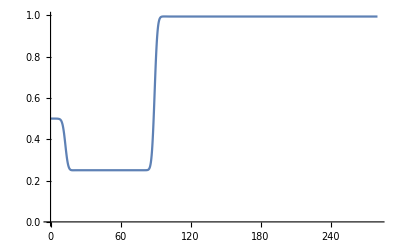

```mathematica
ListLinePlot[fidVsTimeEPR]
```

```mathematica
fidVsTimeEPRCopy=fidVsTimeEPR;
fidVsTimeEPRCopy[[;;,2]]=-Log10[1-fidVsTimeEPRCopy[[;;,2]]];
```

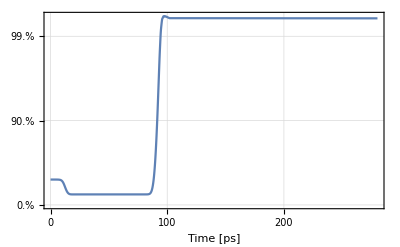

```mathematica
ListLinePlot[fidVsTimeEPRCopy,PlotRange->All,GridLines->Automatic,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,Ceiling[Max[fidVsTimeEPRCopy[[;;,2]]]]}],None},{Table[{i,Style[ToString[i],18]},{i,0,300,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}]]
```

### EPR state preparation and subsequent error estimate ϵ_0

This example illustrates the preparation of the EPR state .

```mathematica
eprTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[epr[[128*4+1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[eprTransformed[[-2*128-1,2]]]]//MatrixForm(*After 1 Pauli-X gates. Before Hadamard and Phase*)
OneBRDM[expansion5to6[eprTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[eprTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.63948×10^-6-0.00119213 ⅈ | 0 | 0 | 0 | 0
-2.63948×10^-6+0.00119213 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.76801×10^-6+0.00119212 ⅈ | 0 | 0
0 | 0 | -2.76801×10^-6-0.00119212 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

(0.50005-1.74266×10^-19 ⅈ | -2.6395×10^-6-0.00119214 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-2.6395×10^-6+0.00119214 ⅈ | 0.499731-3.48022×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-1.74341×10^-19 ⅈ | -2.74909×10^-6+0.0011921 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.74909×10^-6-0.0011921 ⅈ | 0.499735+5.13039×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+3.38697×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.499894+3.06868×10^-16 ⅈ | -0.000156931+0.00118994 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.000156931-0.00118994 ⅈ | 0.499882-2.97875×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-1.69438×10^-19 ⅈ | -2.76149×10^-6+0.00118932 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.76149×10^-6-0.00118932 ⅈ | 0.499735+4.18933×10^-21 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-1.65249×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.499889-7.1286×10^-19 ⅈ | 0.000149435-0.00118697 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.000149435+0.00118697 ⅈ | 0.49988+8.26049×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+8.26683×10^-20 ⅈ | -2.75496×10^-6+0.0011865 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.75496×10^-6-0.0011865 ⅈ | 0.499735+8.25808×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+1.65249×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

The prepared state represents the original α, β, x and y.
6 Pauli-X gates are applied followed by a Hadamard and a Phase gate.
After 6 Pauli-X gates, α and β are slightly modified, becoming α’ and β’, the difference being the errors ϵα and ϵβ.

```mathematica
x=-2.639480862692074*^-6;
y=0.0011921283265124653 ;
α=0.500049858647183;
β=0.4997285700374489;
αp=0.5000498586452028;
βp=0.4997307978740795;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.4998944103958777-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4998890708323476-(α+ϵα+β+ϵβ-2y)/2)
```

-1.98019×10^-12

2.22784×10^-6

6.72162×10^-6

-0.00119087

### EPR state preparation and subsequent error estimate ϵ_1

This example illustrates the preparation of the EPR state .

```mathematica
eprTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[epr[[128*4+1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[eprTransformed[[-2*128-1,2]]]]//MatrixForm(*After 1 Pauli-X gates. Before Hadamard and Phase*)
OneBRDM[expansion5to6[eprTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[eprTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.63948×10^-6-0.00119213 ⅈ | 0 | 0 | 0 | 0
-2.63948×10^-6+0.00119213 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.76801×10^-6+0.00119212 ⅈ | 0 | 0
0 | 0 | -2.76801×10^-6-0.00119212 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

(0.499732-2.7477×10^-18 ⅈ | -3.05547×10^-6+0.00119137 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-3.05547×10^-6-0.00119137 ⅈ | 0.500044-3.74763×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+6.27815×10^-19 ⅈ | -2.76149×10^-6+0.00118932 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.76149×10^-6-0.00118932 ⅈ | 0.499735+2.08155×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+8.3597×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.499882+7.44643×10^-18 ⅈ | 0.000151126-0.00118901 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.000151126+0.00118901 ⅈ | 0.499887-6.20542×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-2.85572×10^-19 ⅈ | -2.75496×10^-6+0.0011865 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.75496×10^-6-0.0011865 ⅈ | 0.499735-4.17775×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-7.03348×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.499876+5.44756×10^-18 ⅈ | -0.000144353+0.00118931 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.000144353-0.00118931 ⅈ | 0.499886+3.51594×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+3.5186×10^-19 ⅈ | -2.74845×10^-6+0.0011837 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.74845×10^-6-0.0011837 ⅈ | 0.499735+3.51487×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+7.03348×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

The prepared state represents the original α, β, x and y.
6 Pauli-X gates are applied followed by a Hadamard and a Phase gate.
After 6 Pauli-X gates, α and β are slightly modified, becoming α’ and β’, the difference being the errors ϵα and ϵβ.

```mathematica
x=-2.639480862692074*^-6;
y=-0.0011921283265124653;
α=0.500049858647183;
β=0.4997285700374489;
αp=0.5000436688552813;
βp=0.4997316949740122;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49988217969096715-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.49987620649005027-(α+ϵα+β+ϵβ-2y)/2)
```

-6.18979×10^-6

3.12494×10^-6

-2.86274×10^-6

0.0012036

### EPR state preparation and subsequent error estimate ϵ_2

This example illustrates the preparation of the EPR state .

```mathematica
eprTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[epr[[128*4+1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[eprTransformed[[-2*128-1,2]]]]//MatrixForm(*After 2 Pauli-X gates. Before Hadamard and Phase*)
OneBRDM[expansion5to6[eprTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[eprTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.63948×10^-6-0.00119213 ⅈ | 0 | 0 | 0 | 0
-2.63948×10^-6+0.00119213 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.76801×10^-6+0.00119212 ⅈ | 0 | 0
0 | 0 | -2.76801×10^-6-0.00119212 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

(0.500035+1.94626×10^-18 ⅈ | -2.99295×10^-6-0.0011887 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-2.99295×10^-6+0.0011887 ⅈ | 0.499736+1.11×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-4.49777×10^-19 ⅈ | -2.75496×10^-6+0.0011865 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.75496×10^-6-0.0011865 ⅈ | 0.499735-7.4544×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-1.19522×10^-18 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.499887+1.69161×10^-16 ⅈ | -0.000143151+0.00118863 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.000143151-0.00118863 ⅈ | 0.499876-1.69702×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+5.97924×10^-19 ⅈ | -2.74845×10^-6+0.0011837 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.74845×10^-6-0.0011837 ⅈ | 0.499735+5.93453×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+1.19138×10^-18 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.499884+8.61671×10^-20 ⅈ | 0.000139998-0.0011863 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.000139998+0.0011863 ⅈ | 0.499877-5.95543×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-5.96004×10^-19 ⅈ | -2.74196×10^-6+0.0011809 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.74196×10^-6-0.0011809 ⅈ | 0.499735-5.95373×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-1.19138×10^-18 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

The prepared state represents the original α, β, x and y.
6 Pauli-X gates are applied followed by a Hadamard and a Phase gate.
After 6 Pauli-X gates, α and β are slightly modified, becoming α’ and β’, the difference being the errors ϵα and ϵβ.

```mathematica
x=-2.639480862692074*^-6;
y=-0.0011921283265124653;
α=0.500049858647183;
β=0.4997285700374489;
αp=0.5000349125460103;
βp=0.4997364294391472;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49988653682954876-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.49988415879500187-(α+ϵα+β+ϵβ-2y)/2)
```

-0.0000149461

7.8594×10^-6

3.50532×10^-6

0.00119364

### EPR state preparation and subsequent error estimate ϵ_3

This example illustrates the preparation of the EPR state .

```mathematica
eprTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[epr[[128*4+1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[eprTransformed[[-2*128-1,2]]]]//MatrixForm(*After 3 Pauli-X gates. Before Hadamard and Phase*)
OneBRDM[expansion5to6[eprTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[eprTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.63948×10^-6-0.00119213 ⅈ | 0 | 0 | 0 | 0
-2.63948×10^-6+0.00119213 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.76801×10^-6+0.00119212 ⅈ | 0 | 0
0 | 0 | -2.76801×10^-6-0.00119212 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

(0.500034+1.47096×10^-19 ⅈ | -1.6299×10^-6-0.00118838 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.6299×10^-6+0.00118838 ⅈ | 0.499735+3.001×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499719-3.98949×10^-18 ⅈ | -8.27425×10^-7-0.00118286 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -8.27425×10^-7+0.00118286 ⅈ | 0.500272+8.0655×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+4.47465×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.500034-5.48102×10^-20 ⅈ | -1.62605×10^-6-0.00118557 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.62605×10^-6+0.00118557 ⅈ | 0.499735-2.23664×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500003-1.54152×10^-16 ⅈ | 0.000280938+0.0011779 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.000280938-0.0011779 ⅈ | 0.499989+1.53288×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-2.78578×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.500034+1.39299×10^-19 ⅈ | -1.62221×10^-6-0.00118277 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.62221×10^-6+0.00118277 ⅈ | 0.499735+1.39215×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499999-4.80205×10^-18 ⅈ | -0.000279761-0.00117441 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.000279761+0.00117441 ⅈ | 0.499989+1.39286×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+2.78578×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

The prepared state represents the original α, β, x and y.
6 Pauli-X gates are applied followed by a Hadamard and a Phase gate.
After 6 Pauli-X gates, α and β are slightly modified, becoming α’ and β’, the difference being the errors ϵα and ϵβ.

```mathematica
x=-2.7680111971088944*^-6;
y=0.0011921283265124653;
α=0.5002640263399474;
β=0.4997345672247591;
αp=0.5002717646217821;
βp=0.4997190765341737;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.5000025673358328-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.49999914941505136-(α+ϵα+β+ϵβ-2y)/2)
```

7.73828×10^-6

-0.0000154907

9.91477×10^-6

-0.00119586

### EPR state preparation and subsequent error estimate ϵ_4

This example illustrates the preparation of the EPR state .

```mathematica
eprTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[epr[[128*4+1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[eprTransformed[[-2*128-1,2]]]]//MatrixForm(*After 6 Pauli-X gates. Before Hadamard and Phase*)
OneBRDM[expansion5to6[eprTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[eprTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.63948×10^-6-0.00119213 ⅈ | 0 | 0 | 0 | 0
-2.63948×10^-6+0.00119213 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.76801×10^-6+0.00119212 ⅈ | 0 | 0
0 | 0 | -2.76801×10^-6-0.00119212 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

(0.500034+7.83482×10^-20 ⅈ | -1.62605×10^-6-0.00118557 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.62605×10^-6+0.00118557 ⅈ | 0.499735-1.05491×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500272+4.15631×10^-18 ⅈ | -3.02617×10^-6+0.00117924 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -3.02617×10^-6-0.00117924 ⅈ | 0.49972-9.18963×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-9.7663×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.500034+4.88368×10^-19 ⅈ | -1.62221×10^-6-0.00118277 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.62221×10^-6+0.00118277 ⅈ | 0.499735+3.89079×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499992+3.8275×10^-16 ⅈ | -0.000279212-0.00117608 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.000279212+0.00117608 ⅈ | 0.499995-3.82258×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+8.77673×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0.500034-4.38866×10^-19 ⅈ | -1.61837×10^-6-0.00117997 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.61837×10^-6+0.00117997 ⅈ | 0.499735-4.38604×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499983+3.72632×10^-19 ⅈ | 0.000290269+0.0011736 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.000290269-0.0011736 ⅈ | 0.499995-4.38832×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-8.77673×10^-19 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

The prepared state represents the original α, β, x and y.
6 Pauli-X gates are applied followed by a Hadamard and a Phase gate.
After 6 Pauli-X gates, α and β are slightly modified, becoming α’ and β’, the difference being the errors ϵα and ϵβ.

```mathematica
x=-2.7680111971088944*^-6;
y=0.0011921283265124653;
α=0.5002640263399474;
β=0.4997345672247591;
αp=0.5002715683664894;
βp=0.49971977278199664;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49999210312747744-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4999830408642205-(α+ϵα+β+ϵβ-2y)/2)
```

7.54203×10^-6

-0.0000147944

-7.99436×10^-7

-0.0011795

### EPR state preparation and subsequent error estimate ϵ_5

This example illustrates the preparation of the EPR state .

```mathematica
eprTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[epr[[128*4+1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[eprTransformed[[-2*128-1,2]]]]//MatrixForm(*After 6 Pauli-X gates. Before Hadamard and Phase*)
OneBRDM[expansion5to6[eprTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[eprTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.63948×10^-6-0.00119213 ⅈ | 0 | 0 | 0 | 0
-2.63948×10^-6+0.00119213 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.76801×10^-6+0.00119212 ⅈ | 0 | 0
0 | 0 | -2.76801×10^-6-0.00119212 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

(0.500034+7.72549×10^-21 ⅈ | -1.62221×10^-6-0.00118277 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.62221×10^-6+0.00118277 ⅈ | 0.499735+2.41367×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500269+8.05571×10^-21 ⅈ | -5.55669×10^-7+0.00117645 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -5.55669×10^-7-0.00117645 ⅈ | 0.499717+2.41312×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.000207962+1.13064×10^-18 ⅈ | 1.93015×10^-6+0.00240592 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.93015×10^-6-0.00240592 ⅈ | 0.999784+7.6984×10^-18 ⅈ)

(0.500034-1.2107×10^-18 ⅈ | -1.61837×10^-6-0.00117997 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.61837×10^-6+0.00117997 ⅈ | 0.499735-1.03284×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499992-6.64207×10^-17 ⅈ | -0.00027921-0.0011733 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.00027921+0.0011733 ⅈ | 0.499995+6.49009×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.000208014-4.54375×10^-22 ⅈ | -1.1906×10^-7+0.00239594 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.1906×10^-7-0.00239594 ⅈ | 0.999788-2.24363×10^-18 ⅈ)

(0.500034+1.12212×10^-18 ⅈ | -1.61454×10^-6-0.00117718 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.61454×10^-6+0.00117718 ⅈ | 0.499735+1.12145×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499983+4.23452×10^-19 ⅈ | 0.000290239+0.00117082 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.000290239-0.00117082 ⅈ | 0.499995+1.12204×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.000208014+4.66805×10^-22 ⅈ | -1.18779×10^-7+0.00239028 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.18779×10^-7-0.00239028 ⅈ | 0.999788+2.24362×10^-18 ⅈ)

The prepared state represents the original α, β, x and y.
6 Pauli-X gates are applied followed by a Hadamard and a Phase gate.
After 6 Pauli-X gates, α and β are slightly modified, becoming α’ and β’, the difference being the errors ϵα and ϵβ.

```mathematica
x=-2.7680111971088944*^-6;
y=0.0011921238218172293;
α=0.5002640263399474;
β=0.4997345672247591;
αp=0.5002690856744367;
βp=0.4997173170243533;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.4999920968673225-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4999830418945939-(α+ϵα+β+ϵβ-2y)/2)
```

5.05933×10^-6

-0.0000172502

1.66353×10^-6

-0.00118196

### EPR state preparation and subsequent error estimate ϵ_6

This example illustrates the preparation of the EPR state .

```mathematica
eprTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[epr[[128*4+1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[eprTransformed[[-2*128-1,2]]]]//MatrixForm(*After 6 Pauli-X gates. Before Hadamard and Phase*)
OneBRDM[expansion5to6[eprTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[eprTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.63948×10^-6-0.00119213 ⅈ | 0 | 0 | 0 | 0
-2.63948×10^-6+0.00119213 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.76801×10^-6+0.00119212 ⅈ | 0 | 0
0 | 0 | -2.76801×10^-6-0.00119212 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

(0.500034+6.67751×10^-19 ⅈ | -1.61837×10^-6-0.00117997 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.61837×10^-6+0.00117997 ⅈ | 0.499735-4.40796×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500269+6.6806×10^-19 ⅈ | -5.54353×10^-7+0.00117367 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -5.54353×10^-7-0.00117367 ⅈ | 0.499717-4.41163×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.999565+1.48043×10^-18 ⅈ | -2.80937×10^-7-0.00480376 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.80937×10^-7+0.00480376 ⅈ | 0.000427445+4.19632×10^-19 ⅈ)

(0.500034-1.1345×10^-19 ⅈ | -1.61453×10^-6-0.00117718 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.61453×10^-6+0.00117718 ⅈ | 0.499735-7.87808×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499992+9.41741×10^-17 ⅈ | -0.000279207-0.00117052 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.000279207+0.00117052 ⅈ | 0.499995-9.16611×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.99956-1.92161×10^-19 ⅈ | 2.1812×10^-6-0.00478726 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.1812×10^-6+0.00478726 ⅈ | 0.000427416-1.20684×10^-22 ⅈ)

(0.500034+9.61482×10^-20 ⅈ | -1.61071×10^-6-0.0011744 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.61071×10^-6+0.0011744 ⅈ | 0.499735+9.60906×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499983-3.07872×10^-19 ⅈ | 0.000290209+0.00116805 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.000290209-0.00116805 ⅈ | 0.499995+9.61407×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.99956+1.92199×10^-19 ⅈ | 2.17604×10^-6-0.00477595 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.17604×10^-6+0.00477595 ⅈ | 0.000427416+8.21849×10^-23 ⅈ)

The prepared state represents the original α, β, x and y.
6 Pauli-X gates are applied followed by a Hadamard and a Phase gate.
After 6 Pauli-X gates, α and β are slightly modified, becoming α’ and β’, the difference being the errors ϵα and ϵβ.

```mathematica
x=-2.7680111971088944*^-6;
y=0.0011921238218172293;
α=0.5002640263399474;
β=0.4997345672247591;
αp=0.5002690856744367;
βp=0.4997173170243533;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.499992090733321-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.499983043001639-(α+ϵα+β+ϵβ-2y)/2)
```

5.05933×10^-6

-0.0000172502

1.6574×10^-6

-0.00118197

### EPR 1-RDM evolution

```mathematica
Table[λvec[expansion5to6[epr[[128i,2]]]],{i,1,4}]
```

{{1.,1.,0.999354,0.000635707,0.,0.},{1.,1.,0.500053,0.000101076,0.,0.},{1.,0.501229,0.500053,0.498766,0.000101152,0.},{1.,0.50122,0.501093,0.498778,0.498688,0.}}

```mathematica
Show[RegionPlot3D[(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Green},MeshStyle->None],
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Blue},MeshStyle->None],
Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[Table[λvec[expansion5to6[epr[[128i,2]]]][[1;;3]],{i,{1,4}}],0.005]]}]]
```

-Graphics3D-

### EPR prep-unprep

This example illustrates the preparation of the EPR state .

```mathematica
eprPuP=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{0,2}},0},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1}
}];
```

Extracting the list of fidelities with a time stamp.

```mathematica
Table[{eprPuP[[128i,1]],fidelity[idealSlater,eprPuP[[128i,2]]]},{i,1,8}]
```

{{25.4,0.500047},{50.8777,0.50005},{76.3554,0.50005},{101.833,0.50005},{127.311,0.50005},{152.789,0.50005},{178.266,0.50005},{203.744,0.987851}}

```mathematica
fidVsTimeEPRPuP=Table[{eprPuP[[i,1]],fidelity[idealSlater,eprPuP[[i,2]]]},{i,1,Dimensions[eprPuP][[1]]}];
```

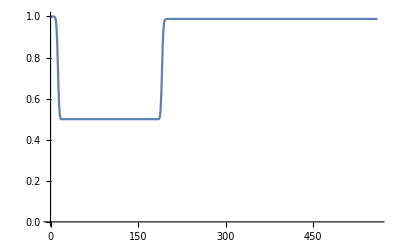

```mathematica
ListLinePlot[fidVsTimeEPRPuP]
```

```mathematica
fidVsTimeEPRPuPCopy=fidVsTimeEPRPuP;
fidVsTimeEPRPuPCopy[[;;,2]]=-Log10[1-fidVsTimeEPRPuPCopy[[;;,2]]];
```

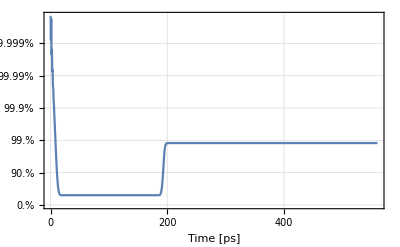

```mathematica
ListLinePlot[fidVsTimeEPRPuPCopy,PlotRange->All,GridLines->Automatic,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,5}],None},{Table[{i,Style[ToString[i],18]},{i,0,500,100}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}]]
```

Evolution of purity

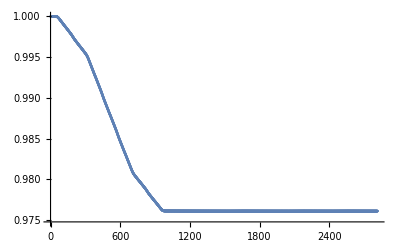

```mathematica
ListPlot[Table[{i,Tr[eprPuP[[i,2]].eprPuP[[i,2]]]//Chop},{i,1,Dimensions[eprPuP][[1]]}]]
```

### GHZ state preparation

This example illustrates the preparation of the EPR state .

```mathematica
ghz=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{222,242}},1},
{-Pi/4,pfactor,{{222,242}},1},
{-Pi/4,pfactor,{{222,242}},1},
{-Pi/4,pfactor,{{222,242}},1}
}];
```

Extracting the list of fidelities with a time stamp.

```mathematica
Table[{ghz[[128i,1]],fidelity[idealGHZ,ghz[[128i,2]]]},{i,1,11}]
```

{{25.4,0.250023},{50.8777,0.250025},{76.3554,0.250025},{101.833,0.250025},{127.311,0.250025},{152.789,0.250025},{178.266,0.985035},{203.744,0.985016},{229.222,0.98501},{254.699,0.985004},{280.177,0.984997}}

```mathematica
fidVsTimeGHZ=Table[{ghz[[i,1]],fidelity[idealGHZ,ghz[[i,2]]]},{i,1,Dimensions[ghz][[1]]}];
```

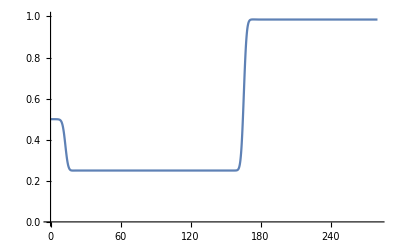

```mathematica
ListLinePlot[fidVsTimeGHZ,PlotRange->{0,1}]
```

```mathematica
fidVsTimeGHZCopy=fidVsTimeGHZ;
fidVsTimeGHZCopy[[;;,2]]=-Log10[1-fidVsTimeGHZCopy[[;;,2]]];
```

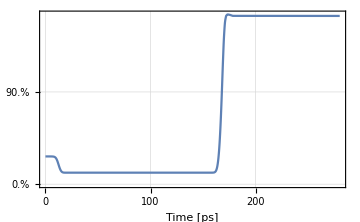

```mathematica
ListLinePlot[fidVsTimeGHZCopy,PlotRange->All,GridLines->Automatic,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,Ceiling[Max[fidVsTimeGHZCopy[[;;,2]]]]}],None},{Table[{i,Style[ToString[i],18]},{i,0,300,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}]]
```

### GHZ state preparation and subsequent error estimate ϵ_0

This example illustrates the preparation of the EPR state .

```mathematica
ghzTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[ghz[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[ghzTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

(0.50005-3.87782×10^-19 ⅈ | -2.62083×10^-6-0.00118371 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-2.62083×10^-6+0.00118371 ⅈ | 0.499729+1.34392×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-3.87948×10^-19 ⅈ | 2.84597×10^-6+1.05446×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.84597×10^-6-1.05446×10^-8 ⅈ | 0.499521+1.42687×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-3.8811×10^-19 ⅈ | -2.75125×10^-6+0.0011916 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.75125×10^-6-0.0011916 ⅈ | 0.499525+1.3469×10^-19 ⅈ)

(0.499894+2.88291×10^-16 ⅈ | -0.000156952+0.00118153 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.000156952-0.00118153 ⅈ | 0.499882-2.89421×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+1.26778×10^-19 ⅈ | 2.83924×10^-6+1.05197×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.83924×10^-6-1.05197×10^-8 ⅈ | 0.499519+1.58721×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473+1.26821×10^-19 ⅈ | -2.76384×10^-6+0.00118882 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.76384×10^-6-0.00118882 ⅈ | 0.499525+1.58888×10^-20 ⅈ)

(0.499889-8.65212×10^-19 ⅈ | 0.000149504-0.00117858 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.000149504+0.00117858 ⅈ | 0.49988-7.13377×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-7.13925×10^-20 ⅈ | 2.83253×10^-6+1.04949×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.83253×10^-6-1.04949×10^-8 ⅈ | 0.499519-7.12862×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-7.14224×10^-20 ⅈ | -2.7573×10^-6+0.00118601 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.7573×10^-6-0.00118601 ⅈ | 0.499525-7.12871×10^-20 ⅈ)

```mathematica
x=-2.6207677586057506*^-6;
y=-0.001183676504878299;
α=0.5000498586944256;
β=0.4997285700807515;
αp=0.5000498586556787;
βp=0.4997285700420295;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49989435383552305-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4998890227659338-(α+ϵα+β+ϵβ-2y)/2)
```

-3.87469×10^-11

-3.8722×10^-11

7.76025×10^-6

0.00118387

### GHZ state preparation and subsequent error estimate ϵ_1

This example illustrates the preparation of the EPR state .

```mathematica
ghzTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[ghz[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[ghzTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

(0.499732-7.97493×10^-19 ⅈ | -3.03277×10^-6+0.00118296 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-3.03277×10^-6-0.00118296 ⅈ | 0.500044+4.59743×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+3.89839×10^-19 ⅈ | 2.83924×10^-6+1.05197×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.83924×10^-6-1.05197×10^-8 ⅈ | 0.499519-3.08211×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473+3.89741×10^-19 ⅈ | -2.76384×10^-6+0.00118882 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.76384×10^-6-0.00118882 ⅈ | 0.499525-3.08079×10^-19 ⅈ)

(0.499882+3.28047×10^-16 ⅈ | 0.000151194-0.00118061 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.000151194+0.00118061 ⅈ | 0.499887-3.37324×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+8.88735×10^-20 ⅈ | 2.83253×10^-6+1.04949×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.83253×10^-6-1.04949×10^-8 ⅈ | 0.499519-4.07842×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473+8.88564×10^-20 ⅈ | -2.75729×10^-6+0.00118601 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.75729×10^-6-0.00118601 ⅈ | 0.499525-4.07846×10^-20 ⅈ)

(0.499876-3.79618×10^-18 ⅈ | -0.000144464+0.00118093 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.000144464-0.00118093 ⅈ | 0.499886-2.40304×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-2.40485×10^-20 ⅈ | 2.82584×10^-6+1.04701×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.82584×10^-6-1.04701×10^-8 ⅈ | 0.499519-2.40127×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-2.40586×10^-20 ⅈ | -2.75075×10^-6+0.0011832 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.75075×10^-6-0.0011832 ⅈ | 0.499525-2.4013×10^-20 ⅈ)

```mathematica
x=-2.6207677586057506*^-6;
y=-0.001183676504878299 ;
α=0.5000498586944256;
β=0.4997285700807515;
αp=0.5000437012981422;
βp=0.4997316543988501;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.4998821932607736-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4998762214720287-(α+ϵα+β+ϵβ-2y)/2)
```

-6.1574×10^-6

3.08432×10^-6

-2.86382×10^-6

0.00119513

### GHZ state preparation and subsequent error estimate ϵ_2

This example illustrates the preparation of the EPR state .

```mathematica
ghzTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[ghz[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[ghzTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

(0.500035-4.25063×10^-18 ⅈ | -2.98304×10^-6-0.00118029 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-2.98304×10^-6+0.00118029 ⅈ | 0.499736+2.35991×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-4.28285×10^-20 ⅈ | 2.83253×10^-6+1.04949×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.83253×10^-6-1.04949×10^-8 ⅈ | 0.499519-2.54647×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-4.26179×10^-20 ⅈ | -2.75729×10^-6+0.00118601 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.75729×10^-6-0.00118601 ⅈ | 0.499525-2.54653×10^-19 ⅈ)

(0.499886+1.68985×10^-16 ⅈ | -0.000143261+0.00118025 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.000143261-0.00118025 ⅈ | 0.499876-1.67123×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264+1.48733×10^-19 ⅈ | 2.82584×10^-6+1.04701×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.82584×10^-6-1.04701×10^-8 ⅈ | 0.499519-3.34063×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473+1.48745×10^-19 ⅈ | -2.75076×10^-6+0.0011832 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.75076×10^-6-0.0011832 ⅈ | 0.499525-3.3417×10^-20 ⅈ)

(0.499884+8.53639×10^-18 ⅈ | 0.000140145-0.00117794 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.000140145+0.00117794 ⅈ | 0.499877-5.76496×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500264-5.76942×10^-20 ⅈ | 2.81916×10^-6+1.04453×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.81916×10^-6-1.04453×10^-8 ⅈ | 0.499519-5.76083×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-5.77183×10^-20 ⅈ | -2.74425×10^-6+0.00118041 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.74425×10^-6-0.00118041 ⅈ | 0.499525-5.7609×10^-20 ⅈ)

```mathematica
x=-2.6207677586057506*^-6;
y=-0.001183676504878299 ;
α=0.5000498586944256;
β=0.4997285700807515;
αp=0.5000350075274167;
βp=0.49973635132103944;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49988648865795576-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4998840917589201-(α+ϵα+β+ϵβ-2y)/2)
```

-0.0000148512

7.78124×10^-6

3.43×10^-6

0.00118526

### GHZ state preparation and subsequent error estimate ϵ_3

This example illustrates the preparation of the EPR state .

```mathematica
ghzTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[ghz[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[ghzTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

(0.500034+6.33665×10^-19 ⅈ | -1.60142×10^-6-0.00118 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.60142×10^-6+0.00118 ⅈ | 0.499735+6.55838×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.49951+1.45608×10^-18 ⅈ | 4.76747×10^-6+1.7804×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 4.76747×10^-6-1.7804×10^-6 ⅈ | 0.500266-9.82655×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473+6.34173×10^-19 ⅈ | -2.75076×10^-6+0.0011832 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.75076×10^-6-0.0011832 ⅈ | 0.499525+6.55373×10^-19 ⅈ)

(0.500034-4.32969×10^-19 ⅈ | -1.59763×10^-6-0.00117721 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59763×10^-6+0.00117721 ⅈ | 0.499735-6.44445×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499882-5.13722×10^-17 ⅈ | 0.00037572-4.55807×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.00037572+4.55807×10^-6 ⅈ | 0.499894+5.06351×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-4.33539×10^-19 ⅈ | -2.74423×10^-6+0.00118041 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.74423×10^-6-0.00118041 ⅈ | 0.499525-6.44175×10^-19 ⅈ)

(0.500034+5.38895×10^-19 ⅈ | -1.59387×10^-6-0.00117443 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59387×10^-6+0.00117443 ⅈ | 0.499735+5.38572×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499879+1.4925×10^-19 ⅈ | -0.000375014+5.66589×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.000375014-5.66589×10^-6 ⅈ | 0.499894+5.38744×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473+5.39368×10^-19 ⅈ | -2.73775×10^-6+0.00117762 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.73775×10^-6-0.00117762 ⅈ | 0.499525+5.38346×10^-19 ⅈ)

```mathematica
x=2.8458978366970725*^-6;
y=1.0544394826010129*^-8;
α=0.5002640263872103;
β=0.4995192707586027;
αp=0.5002659424947119;
βp=0.49950956199069524;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49988188558031077-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.49987854164800705-(α+ϵα+β+ϵβ-2y)/2)
```

1.91611×10^-6

-9.70877×10^-6

-8.71256×10^-6

9.20005×10^-6

### GHZ state preparation and subsequent error estimate ϵ_4

This example illustrates the preparation of the EPR state .

```mathematica
ghzTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[ghz[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[ghzTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

(0.500034-1.88826×10^-18 ⅈ | -1.59763×10^-6-0.00117721 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59763×10^-6+0.00117721 ⅈ | 0.499735-6.7409×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.50026-2.28445×10^-18 ⅈ | 2.54242×10^-6-3.59586×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.54242×10^-6+3.59586×10^-6 ⅈ | 0.499516+4.75681×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-1.88885×10^-18 ⅈ | -2.74423×10^-6+0.00118041 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.74423×10^-6-0.00118041 ⅈ | 0.499525-6.73817×10^-19 ⅈ)

(0.500034+1.2815×10^-18 ⅈ | -1.59382×10^-6-0.00117443 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59382×10^-6+0.00117443 ⅈ | 0.499735+1.25422×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.49988+9.59415×10^-17 ⅈ | -0.000374655+4.52385×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.000374655-4.52385×10^-6 ⅈ | 0.499892-8.76227×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473+1.2825×10^-18 ⅈ | -2.73775×10^-6+0.00117762 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.73775×10^-6-0.00117762 ⅈ | 0.499525+1.2538×10^-18 ⅈ)

(0.500034-1.26824×10^-18 ⅈ | -1.59005×10^-6-0.00117165 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59005×10^-6+0.00117165 ⅈ | 0.499735-1.26748×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499871+4.82155×10^-19 ⅈ | 0.000373439-4.67038×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.000373439+4.67038×10^-6 ⅈ | 0.499892-1.26788×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500473-1.26935×10^-18 ⅈ | -2.73129×10^-6+0.00117484 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.73129×10^-6-0.00117484 ⅈ | 0.499525-1.26695×10^-18 ⅈ)

```mathematica
x=2.8458978366970725*^-6;
y=1.0544394826010129*^-8;
α=0.5002640263872103;
β=0.4995192707586027;
αp=0.5002600702348592;
βp=0.49951596150139044;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.4998800607404812-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.49987093408533434-(α+ϵα+β+ϵβ-2y)/2)
```

-3.95615×10^-6

-3.30926×10^-6

-0.000010801

0.0000170712

### GHZ state preparation and subsequent error estimate ϵ_5

This example illustrates the preparation of the EPR state .

```mathematica
ghzTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[ghz[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[ghzTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

(0.500034+4.66367×10^-19 ⅈ | -1.59382×10^-6-0.00117443 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59382×10^-6+0.00117443 ⅈ | 0.499735+1.46733×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500258+4.67325×10^-19 ⅈ | 4.99375×10^-6-3.58348×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 4.99375×10^-6+3.58348×10^-6 ⅈ | 0.499514+1.46645×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.49951-3.64199×10^-18 ⅈ | -7.8264×10^-7-0.00117577 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -7.8264×10^-7+0.00117577 ⅈ | 0.500481-1.43451×10^-18 ⅈ)

(0.500034-9.6727×10^-19 ⅈ | -1.59005×10^-6-0.00117165 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59005×10^-6+0.00117165 ⅈ | 0.499735-9.53444×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.49988-2.78192×10^-17 ⅈ | -0.000374653+4.51513×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.000374653-4.51513×10^-6 ⅈ | 0.499892+2.3898×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.499512-9.53013×10^-19 ⅈ | -2.87409×10^-6-0.001173 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.87409×10^-6+0.001173 ⅈ | 0.500483-9.68139×10^-19 ⅈ)

(0.500034+9.60646×10^-19 ⅈ | -1.58629×10^-6-0.00116888 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.58629×10^-6+0.00116888 ⅈ | 0.499735+9.60071×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499871+1.636×10^-18 ⅈ | 0.000373439-4.66353×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.000373439+4.66353×10^-6 ⅈ | 0.499892+9.60373×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.499512+9.59643×10^-19 ⅈ | -2.86731×10^-6-0.00117023 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.86731×10^-6+0.00117023 ⅈ | 0.500483+9.61509×10^-19 ⅈ)

```mathematica
x=2.8458978366970725*^-6;
y=1.0544394826010129*^-8;
α=0.5002640263872103;
β=0.4995192707586027;
αp=0.5002576052691815;
βp=0.4995135001937814;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49988006510251654-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4998709458144599-(α+ϵα+β+ϵβ-2y)/2)
```

-6.42112×10^-6

-5.77056×10^-6

-8.33353×10^-6

0.0000145964

### GHZ state preparation and subsequent error estimate ϵ_6

This example illustrates the preparation of the EPR state .

```mathematica
ghzTransformed=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[ghz[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[ghzTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[ghzTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

(0.500034-1.74419×10^-18 ⅈ | -1.59005×10^-6-0.00117165 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.59005×10^-6+0.00117165 ⅈ | 0.499735-1.16971×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500258-1.74434×10^-18 ⅈ | 4.98193×10^-6-3.57501×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 4.98193×10^-6+3.57501×10^-6 ⅈ | 0.499514-1.16957×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500481-1.11926×10^-17 ⅈ | -3.00377×10^-6+0.00117116 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -3.00377×10^-6-0.00117116 ⅈ | 0.499511+1.6218×10^-17 ⅈ)

(0.500034+1.45726×10^-18 ⅈ | -1.58629×10^-6-0.00116888 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.58629×10^-6+0.00116888 ⅈ | 0.499735+1.17577×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.49988-3.90714×10^-17 ⅈ | -0.000374652+4.50645×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.000374652-4.50645×10^-6 ⅈ | 0.499892+3.97395×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500478+1.45855×10^-18 ⅈ | -5.42042×10^-7+0.00116839 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -5.42042×10^-7-0.00116839 ⅈ | 0.499508+1.17511×10^-18 ⅈ)

(0.500034-1.31694×10^-18 ⅈ | -1.58254×10^-6-0.00116612 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.58254×10^-6+0.00116612 ⅈ | 0.499735-1.31615×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499871+2.43605×10^-19 ⅈ | 0.000373438-4.65669×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.000373438+4.65669×10^-6 ⅈ | 0.499892-1.31656×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.500478-1.31811×10^-18 ⅈ | -5.40769×10^-7+0.00116563 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -5.40769×10^-7-0.00116563 ⅈ | 0.499508-1.31555×10^-18 ⅈ)

```mathematica
x=2.8458978366970725*^-6;
y=1.0544394826010129*^-8;
α=0.5002640263872103;
β=0.4995192707586027;
αp=0.5002576052993911;
βp=0.4995135002199912;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.499880069392992-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4998709574940128-(α+ϵα+β+ϵβ-2y)/2)
```

-6.42109×10^-6

-5.77054×10^-6

-8.32926×10^-6

0.0000145847

### GHZ 1-RDM evolution

```mathematica
Table[λvec[expansion5to6[ghz[[128i,2]]]],{i,1,7}]
```

{{1.,1.,0.999354,0.000635707,0.,0.},{1.,1.,0.500053,0.000101076,0.,0.},{1.,0.501229,0.500053,0.498766,0.000101152,0.},{1.,0.50122,0.501093,0.498778,0.498688,0.},{1.,0.501089,0.500264,0.498689,0.000103912,0.},{0.50129,0.501087,0.500264,0.498705,0.498692,0.000103965},{0.501282,0.501084,0.500264,0.499521,0.498717,0.498695}}

```mathematica
Show[RegionPlot3D[(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Green},MeshStyle->None,TicksStyle->Directive[22]],
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Blue},MeshStyle->None],
Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{1,4}}],0.005]],Arrow[Tube[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{4,7}}],0.005]]}]]
```

-Graphics3D-

### GHZ prep-unprep

This example illustrates the preparation of the EPR state .

```mathematica
ghzPuP=multigateMultiqubit[{
{Pi/8,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{22,24}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{0,2}},0},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1},
{Pi/8,pfactor,{{0,2}},1}
}];
```

Extracting the list of fidelities with a time stamp.

```mathematica
Table[{ghzPuP[[128i,1]],fidelity[idealSlater,ghzPuP[[128i,2]]]},{i,1,14}]
```

{{25.4,0.500047},{50.8777,0.50005},{76.3554,0.50005},{101.833,0.50005},{127.311,0.50005},{152.789,0.50005},{178.266,0.50005},{203.744,0.50005},{229.222,0.50005},{254.699,0.50005},{280.177,0.50005},{305.655,0.50005},{331.132,0.50005},{356.61,0.970391}}

```mathematica
fidVsTimeGHZPuP=Table[{ghzPuP[[i,1]],fidelity[idealSlater,ghzPuP[[i,2]]]},{i,1,Dimensions[ghzPuP][[1]]}];
```

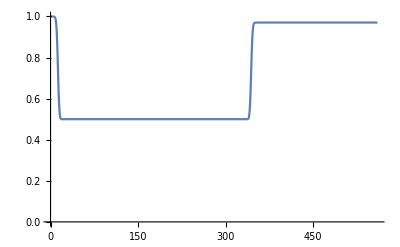

```mathematica
ListLinePlot[fidVsTimeGHZPuP,PlotRange->{0,1}]
```

```mathematica
fidVsTimeGHZPuPCopy=fidVsTimeGHZPuP;
fidVsTimeGHZPuPCopy[[;;,2]]=-Log10[1-fidVsTimeGHZPuPCopy[[;;,2]]];
```

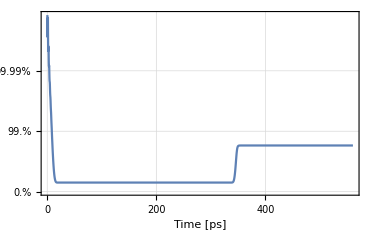

```mathematica
ListLinePlot[fidVsTimeGHZPuPCopy,PlotRange->All,GridLines->Automatic,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,5}],None},{Table[{i,Style[ToString[i],18]},{i,0,500,100}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}]]
```

Evolution of purity

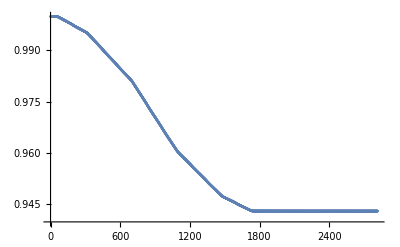

```mathematica
ListPlot[Table[{i,Tr[ghzPuP[[i,2]].ghzPuP[[i,2]]]//Chop},{i,1,Dimensions[ghzPuP][[1]]}]]
```

### W state preparation

This example illustrates the preparation of the EPR state .

```mathematica
w=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0}
}];
```

Extracting the list of fidelities with a time stamp.

```mathematica
Table[{w[[128i,1]],fidelity[idealW,w[[128i,2]]]},{i,1,11}]
```

{{25.4,0.222189},{50.8777,0.0000462037},{76.3554,0.000046222},{101.833,0.111057},{127.311,0.111058},{152.789,0.111058},{178.266,0.111058},{203.744,0.0000911583},{229.222,0.0000911372},{254.699,0.0000474614},{280.177,0.97411}}

```mathematica
fidVsTimeW=Table[{w[[i,1]],fidelity[idealW,w[[i,2]]]},{i,1,Dimensions[w][[1]]}];
```

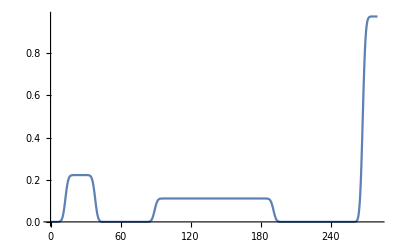

```mathematica
ListLinePlot[fidVsTimeW,PlotRange->All]
```

```mathematica
fidVsTimeWCopy=fidVsTimeW;
fidVsTimeWCopy[[;;,2]]=-Log10[1-fidVsTimeWCopy[[;;,2]]];
```

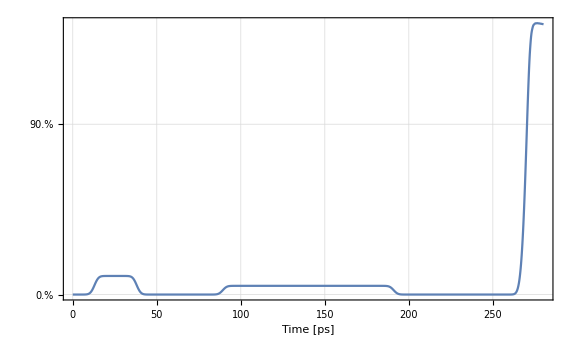

```mathematica
ListLinePlot[fidVsTimeWCopy,PlotRange->All,GridLines->Automatic,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,Ceiling[Max[fidVsTimeEPRCopy[[;;,2]]]]}],None},{Table[{i,Style[ToString[i],18]},{i,0,300,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}]]
```

### W state preparation and subsequent error estimate ϵ_0

This example illustrates the preparation of the EPR state .

```mathematica
wTransformed=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[w[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[wTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[wTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[wTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

(0.665945+3.88888×10^-18 ⅈ | 0.0000242782+0.000849171 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000242782-0.000849171 ⅈ | 0.333486+7.94172×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606-4.87756×10^-19 ⅈ | -4.64555×10^-7+0.000785848 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.64555×10^-7-0.000785848 ⅈ | 0.333242-2.22261×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696-4.92073×10^-19 ⅈ | -1.90468×10^-6+0.000786981 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.90468×10^-6-0.000786981 ⅈ | 0.333039-2.17919×10^-19 ⅈ)

(0.499702-2.07333×10^-16 ⅈ | -0.16602-0.000248525 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.16602+0.000248525 ⅈ | 0.499723+2.09046×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606+6.29823×10^-19 ⅈ | -4.63492×10^-7+0.00078399 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.63492×10^-7-0.00078399 ⅈ | 0.333242+2.36602×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+6.30074×10^-19 ⅈ | -1.9002×10^-6+0.000785121 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.9002×10^-6-0.000785121 ⅈ | 0.333039+2.36458×10^-19 ⅈ)

(0.499696-3.92496×10^-18 ⅈ | 0.165628-0.000547172 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.165628+0.000547172 ⅈ | 0.499722-4.33026×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606-5.77636×10^-19 ⅈ | -4.62398×10^-7+0.000782138 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.62398×10^-7-0.000782138 ⅈ | 0.333242-2.88765×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696-5.77943×10^-19 ⅈ | -1.89573×10^-6+0.000783266 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.89573×10^-6-0.000783266 ⅈ | 0.333039-2.88589×10^-19 ⅈ)

```mathematica
x=0.000024278233919256764;
y=0.0008491707646916813;
α=0.6659448841274344;
β=0.33348612932195587;
αp=0.6659448841274344;
βp=0.33348612932195587;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49970205850296695-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.499696082455274-(α+ϵα+β+ϵβ-2y)/2)
```

0.

0.

-0.0000377265

-0.000829746

### W state preparation and subsequent error estimate ϵ_1

This example illustrates the preparation of the EPR state .

```mathematica
wTransformed=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[w[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[wTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[wTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[wTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

(0.333549+6.85228×10^-18 ⅈ | 0.0000240196-0.0000479159 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000240196+0.0000479159 ⅈ | 0.665878-3.34364×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606+8.21426×10^-19 ⅈ | -4.63492×10^-7+0.00078399 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.63492×10^-7-0.00078399 ⅈ | 0.333242+2.27997×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+3.79679×10^-19 ⅈ | -1.9002×10^-6+0.000785121 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.9002×10^-6-0.000785121 ⅈ | 0.333039+6.69859×10^-19 ⅈ)

(0.499666-2.8017×10^-17 ⅈ | 0.165953-0.000548836 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.165953+0.000548836 ⅈ | 0.499753+2.63977×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606-6.57889×10^-19 ⅈ | -4.62434×10^-7+0.000782138 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.62434×10^-7-0.000782138 ⅈ | 0.333242-2.54966×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696-6.05219×10^-19 ⅈ | -1.89572×10^-6+0.000783266 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.89572×10^-6-0.000783266 ⅈ | 0.333039-3.07761×10^-19 ⅈ)

(0.499663-1.40684×10^-18 ⅈ | -0.165555+0.00134509 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.165555-0.00134509 ⅈ | 0.499754+4.56266×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606+6.08598×10^-19 ⅈ | -4.61341×10^-7+0.000780289 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.61341×10^-7-0.000780289 ⅈ | 0.333242+3.04243×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+6.08922×10^-19 ⅈ | -1.89125×10^-6+0.000781415 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.89125×10^-6-0.000781415 ⅈ | 0.333039+3.04058×10^-19 ⅈ)

```mathematica
x=0.000024278233919256764;
y=0.0008491707646916813;
α=0.6659448841274344;
β=0.33348612932195587;
αp=0.665878413940578;
βp=0.3335490929611579;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49966629269641555-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.49966288867734554-(α+ϵα+β+ϵβ-2y)/2)
```

-0.0000664702

0.0000629636

-0.000071739

-0.000798306

### W state preparation and subsequent error estimate ϵ_2

This example illustrates the preparation of the EPR state .

```mathematica
wTransformed=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/8,pfactor,{{0,2}},0},
{0,pfactor,{{0,2}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[w[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[wTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[wTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[wTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

(0.665806-5.85591×10^-18 ⅈ | 0.000025801-0.000749151 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.000025801+0.000749151 ⅈ | 0.333614+5.38292×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606-1.04344×10^-18 ⅈ | -4.62434×10^-7+0.000782138 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.62434×10^-7-0.000782138 ⅈ | 0.333242+2.79059×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+3.91542×10^-19 ⅈ | -1.89572×10^-6+0.000783266 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.89572×10^-6-0.000783266 ⅈ | 0.333039-1.15607×10^-18 ⅈ)

(0.499702-1.04277×10^-16 ⅈ | -0.165877+0.00134474 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.165877-0.00134474 ⅈ | 0.499714+1.03171×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606+7.43877×10^-19 ⅈ | -4.6138×10^-7+0.000780289 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.6138×10^-7-0.000780289 ⅈ | 0.333242+2.54785×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+7.44147×10^-19 ⅈ | -1.89125×10^-6+0.000781415 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.89125×10^-6-0.000781415 ⅈ | 0.333039+2.54631×10^-19 ⅈ)

(0.499702+1.51068×10^-18 ⅈ | 0.165478-0.00214018 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.165478+0.00214018 ⅈ | 0.499715-4.99104×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666606-6.65792×10^-19 ⅈ | -4.6029×10^-7+0.000778445 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.6029×10^-7-0.000778445 ⅈ | 0.333242-3.32835×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696-6.66146×10^-19 ⅈ | -1.88679×10^-6+0.000779568 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.88679×10^-6-0.000779568 ⅈ | 0.333039-3.32632×10^-19 ⅈ)

```mathematica
x=0.000024278233919256764;
y=0.0008491707646916813;
α=0.6659448841274344;
β=0.33348612932195587;
αp=0.6658056712322508;
βp=0.3336142495806395;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.49970204066082785-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.49970234361280175-(α+ϵα+β+ϵβ-2y)/2)
```

-0.000139213

0.00012812

-0.000032198

-0.000841554

### W state preparation and subsequent error estimate ϵ_3

This example illustrates the preparation of the EPR state .

```mathematica
wTransformed=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[w[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[wTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[wTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[wTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

(0.665806+5.34044×10^-19 ⅈ | 0.0000237697-0.00074784 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000237697+0.00074784 ⅈ | 0.333618+2.95627×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.333447-5.25411×10^-19 ⅈ | -1.81467×10^-6+0.0000213648 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -1.81467×10^-6-0.0000213648 ⅈ | 0.666399+3.09133×10^-20 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+8.65435×10^-19 ⅈ | -1.89125×10^-6+0.000781415 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.89125×10^-6-0.000781415 ⅈ | 0.333039-3.53487×10^-20 ⅈ)

(0.665806-5.79652×10^-19 ⅈ | 0.0000237135-0.000746073 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000237135+0.000746073 ⅈ | 0.333618-1.26472×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499969-4.93024×10^-17 ⅈ | 0.166331-0.000620199 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.166331+0.000620199 ⅈ | 0.499871+4.71727×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696-4.03205×10^-19 ⅈ | -1.88679×10^-6+0.000779568 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.88679×10^-6-0.000779568 ⅈ | 0.333039-3.03396×10^-19 ⅈ)

(0.665806+4.70459×10^-19 ⅈ | 0.0000236574-0.00074431 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000236574+0.00074431 ⅈ | 0.333618+2.35735×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.499964-1.01168×10^-19 ⅈ | -0.165937+0.00141673 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.165937-0.00141673 ⅈ | 0.499872+3.5321×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+4.71275×10^-19 ⅈ | -1.88234×10^-6+0.000777726 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.88234×10^-6-0.000777726 ⅈ | 0.333039+2.35326×10^-19 ⅈ)

```mathematica
x=-4.6455469522440385*^-7;
y=0.000785847620756578;
α=0.6666062053643353;
β=0.33324162019919035;
αp=0.6663994125852601;
βp=0.3334472176186197;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.4999689097405339-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.4999636232977468-(α+ϵα+β+ϵβ-2y)/2)
```

-0.000206793

0.000205597

0.0000460592

-0.000826156

### W state preparation and subsequent error estimate ϵ_4

This example illustrates the preparation of the EPR state .

```mathematica
wTransformed=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[w[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[wTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[wTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[wTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

(0.665806-1.14383×10^-18 ⅈ | 0.0000237135-0.000746073 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000237135+0.000746073 ⅈ | 0.333618-6.90326×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666466-3.77154×10^-18 ⅈ | -4.08405×10^-7-0.000820805 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -4.08405×10^-7+0.000820805 ⅈ | 0.333374-2.5063×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696-1.86257×10^-18 ⅈ | -1.88679×10^-6+0.000779568 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.88679×10^-6-0.000779568 ⅈ | 0.333039+2.79423×10^-20 ⅈ)

(0.665806+1.20985×10^-18 ⅈ | 0.0000236574-0.00074431 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000236574+0.00074431 ⅈ | 0.333618+6.12049×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500005+1.7922×10^-16 ⅈ | -0.16626+0.00141685 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.16626-0.00141685 ⅈ | 0.499831-1.71867×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696+1.21196×10^-18 ⅈ | -1.88235×10^-6+0.000777726 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.88235×10^-6-0.000777726 ⅈ | 0.333039+6.10987×10^-19 ⅈ)

(0.665806-1.21373×10^-18 ⅈ | 0.0000236015-0.000742551 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000236015+0.000742551 ⅈ | 0.333618-6.08169×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500004+2.82259×10^-18 ⅈ | 0.165854-0.00221361 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.165854+0.00221361 ⅈ | 0.499831-9.11168×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66696-1.21584×10^-18 ⅈ | -1.87789×10^-6+0.000775888 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.87789×10^-6-0.000775888 ⅈ | 0.333039-6.07114×10^-19 ⅈ)

```mathematica
x=-4.6455469522440385*^-7;
y=0.000785847620756578;
α=0.6666062053643353;
β=0.33324162019919035;
αp=0.6664657950653997;
βp=0.3333741228260458;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.5000047435893461-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.5000042746428541-(α+ϵα+β+ϵβ-2y)/2)
```

-0.00014041

0.000132503

0.0000852492

-0.000870163

### W state preparation and subsequent error estimate ϵ_5

This example illustrates the preparation of the EPR state .

```mathematica
wTransformed=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[w[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[wTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[wTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[wTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

(0.665806+7.39688×10^-19 ⅈ | 0.0000236574-0.00074431 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000236574+0.00074431 ⅈ | 0.333618+1.46862×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666465+1.33066×10^-18 ⅈ | -1.81987×10^-6-0.000818621 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -1.81987×10^-6+0.000818621 ⅈ | 0.333377+8.77874×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.333098+1.22451×10^-17 ⅈ | 9.16898×10^-8+0.0000253765 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 9.16898×10^-8-0.0000253765 ⅈ | 0.666893-1.40033×10^-17 ⅈ)

(0.665806-1.42637×10^-18 ⅈ | 0.0000236015-0.000742551 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000236015+0.000742551 ⅈ | 0.333618-7.36923×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500005+4.49379×10^-16 ⅈ | -0.16626+0.00141492 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.16626-0.00141492 ⅈ | 0.499831-4.55597×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.3331-7.35778×10^-19 ⅈ | -2.03867×10^-6+0.0000238781 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.03867×10^-6-0.0000238781 ⅈ | 0.666896-1.42878×10^-18 ⅈ)

(0.665806+1.44118×10^-18 ⅈ | 0.0000235458-0.000740796 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000235458+0.000740796 ⅈ | 0.333618+7.22137×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500004-9.23894×10^-19 ⅈ | 0.165854-0.00221168 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.165854+0.00221168 ⅈ | 0.499831+1.08192×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.3331+7.21015×10^-19 ⅈ | -2.03385×10^-6+0.0000238216 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.03385×10^-6-0.0000238216 ⅈ | 0.666896+1.44354×10^-18 ⅈ)

```mathematica
x=-4.6455469522440385*^-7;
y=0.000785847620756578;
α=0.6666062053643353;
β=0.33324162019919035;
αp=0.6664653494250357;
βp=0.333377400130014;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.5000047352021431-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.5000042698116771-(α+ϵα+β+ϵβ-2y)/2)
```

-0.000140856

0.00013578

0.000083825

-0.000868743

### W state preparation and subsequent error estimate ϵ_6

This example illustrates the preparation of the EPR state .

```mathematica
wTransformed=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,20}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/4,pfactor,{{0,200}},0},
{-Pi/8,pfactor,{{0,20}},0},
{0,pfactor,{{0,20}},0}
}];
```

```mathematica
OneBRDM[expansion5to6[w[[-1,2]]]]//Chop//MatrixForm
OneBRDM[expansion5to6[wTransformed[[-2*128-1,2]]]]//MatrixForm(*Before Hadamard and Phase*)
OneBRDM[expansion5to6[wTransformed[[-128-1,2]]]]//MatrixForm(*After Hadamard and before Phase*)
OneBRDM[expansion5to6[wTransformed[[-1,2]]]]//MatrixForm(*After Phase*)
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

(0.665806-2.28376×10^-18 ⅈ | 0.0000236015-0.000742551 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000236015+0.000742551 ⅈ | 0.333618-6.8094×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.666465-1.88626×10^-18 ⅈ | -1.81563×10^-6-0.000816686 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -1.81563×10^-6+0.000816686 ⅈ | 0.333377-1.07957×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.66682-1.27191×10^-17 ⅈ | -2.14392×10^-6-0.000827629 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.14392×10^-6+0.000827629 ⅈ | 0.333172+9.73023×10^-18 ⅈ)

(0.665806+1.86768×10^-18 ⅈ | 0.0000235457-0.000740796 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000235457+0.000740796 ⅈ | 0.333618+9.89584×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500005+4.34587×10^-16 ⅈ | -0.16626+0.00141299 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.16626-0.00141299 ⅈ | 0.499831-4.33815×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.666817+1.87067×10^-18 ⅈ | 3.10775×10^-7-0.00082392 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 3.10775×10^-7+0.00082392 ⅈ | 0.33317+9.88256×10^-19 ⅈ)

(0.665806-1.90352×10^-18 ⅈ | 0.0000234901-0.000739045 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000234901+0.000739045 ⅈ | 0.333618-9.53803×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.500004+6.45946×10^-19 ⅈ | 0.165854-0.00220975 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.165854+0.00220975 ⅈ | 0.499831-1.429×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.666817-1.90641×10^-18 ⅈ | 3.1005×10^-7-0.000821973 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 3.1005×10^-7+0.000821973 ⅈ | 0.33317-9.52523×10^-19 ⅈ)

```mathematica
x=-4.6455469522440385*^-7;
y=0.000785847620756578;
α=0.6666062053643353;
β=0.33324162019919035;
αp=0.66646534937961;
βp=0.3333774001016135;

ϵα=αp-α
ϵβ=βp-β
ϵx=0.5000047266670657-(α+ϵα+β+ϵβ+2x)/2
ϵy=-(0.5000042649180632-(α+ϵα+β+ϵβ-2y)/2)
```

-0.000140856

0.00013578

0.0000838165

-0.000868738

### W 1-RDM evolution

```mathematica
Table[λvec[expansion5to6[w[[128i,2]]]],{i,1,11}]
```

{{1.,1.,0.99938,0.000609979,0.,0.},{1.,1.,0.333429,0.000134771,0.,0.},{1.,0.872255,0.333429,0.127738,0.000134858,0.},{1.,0.871556,0.869925,0.129779,0.12844,0.},{1.,0.869233,0.666819,0.130477,0.0000683195,0.},{0.868537,0.666962,0.666819,0.333035,0.131173,0.000068373},{0.867844,0.666962,0.66682,0.333037,0.333034,0.131866},{0.666962,0.66682,0.333429,0.333037,0.333033,0.000404526},{0.666962,0.666608,0.333429,0.333243,0.333037,0.000404457},{0.666962,0.666608,0.666024,0.333417,0.33324,0.333037},{0.666962,0.666608,0.665947,0.333484,0.33324,0.333037}}

```mathematica
Show[RegionPlot3D[(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Green},MeshStyle->None,TicksStyle->Directive[22]],
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Blue},MeshStyle->None],
Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[Table[λvec[expansion5to6[w[[128i,2]]]][[1;;3]],{i,{1,4,7,10}}],0.005]]}]]
```

-Graphics3D-

```mathematica
Show[(*RegionPlot3D[1≥x≥0.5&&1≥y≥0.5&&1≥z≥0.5&&x≥y&&y≥z&&x≥z,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->Opacity[0.1],MeshStyle->None],*)
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Green},MeshStyle->None],
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Blue},MeshStyle->None],
Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[Table[λvec[expansion5to6[w[[128i,2]]]][[1;;3]],{i,{1,4,7,10}}],0.005]]}]]
```

-Graphics3D-

### W prep-unprep

This example illustrates the preparation of the EPR state .

```mathematica
wPuP=multigateMultiqubit[{
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{2,4}},0},
{Pi/8,pfactor,{{4,24}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{-Pi/4,pfactor,{{22,42}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{0,2}},0},
{-Pi/4,pfactor,{{22,24},{202,204}},0},
{-Pi/4,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{2,4},{222,224}},0},
{-Pi/4,pfactor,{{222,242}},0},
{-Pi/4,pfactor,{{42,242}},0},
{-Pi/4,pfactor,{{22,42}},0},
{Pi/4,pfactor,{{2,4},{22,24}},0},
{Pi/8,pfactor,{{4,24}},0},
{-Pi/4,pfactor,{{2,4}},0},
{ArcCos[1/Sqrt[3]]/2,pfactor,{{0,2}},0}
}];
```

Extracting the list of fidelities with a time stamp.

```mathematica
Table[{wPuP[[128i,1]],fidelity[idealSlater,wPuP[[128i,2]]]},{i,1,22}]
```

{{25.4,0.333422},{50.8777,0.333425},{76.3554,0.333425},{101.833,0.333425},{127.311,0.333425},{152.789,0.333425},{178.266,0.333425},{203.744,0.333425},{229.222,0.333425},{254.699,0.333425},{280.177,0.000219659},{305.655,0.333264},{331.132,0.333264},{356.61,0.333264},{382.088,0.333264},{407.566,0.333264},{433.043,0.333264},{458.521,0.333264},{483.999,0.333264},{509.476,0.333264},{534.954,0.333264},{560.432,0.949069}}

```mathematica
fidVsTimeWPuP=Table[{wPuP[[i,1]],fidelity[idealSlater,wPuP[[i,2]]]},{i,1,Dimensions[wPuP][[1]]}];
```

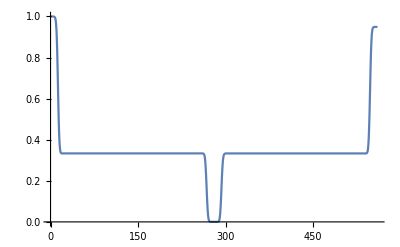

```mathematica
ListLinePlot[fidVsTimeWPuP,PlotRange->All]
```

```mathematica
fidVsTimeWPuPCopy=fidVsTimeWPuP;
fidVsTimeWPuPCopy[[;;,2]]=-Log10[1-fidVsTimeWPuPCopy[[;;,2]]];
```

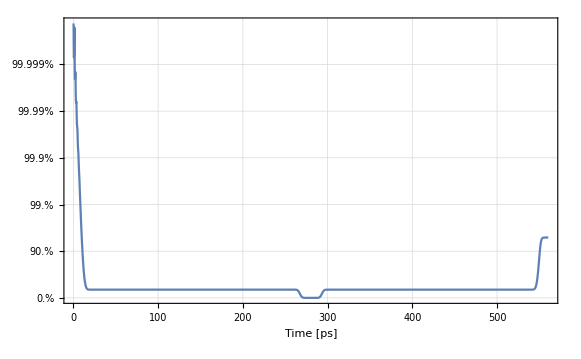

```mathematica
ListLinePlot[fidVsTimeWPuPCopy,PlotRange->All,GridLines->Automatic,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,5}],None},{Table[{i,Style[ToString[i],18]},{i,0,500,100}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}]]
```

Evolution of purity

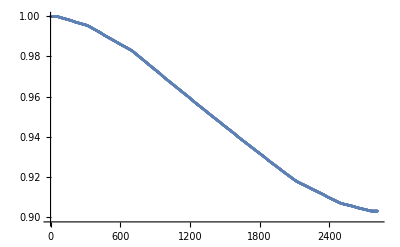

```mathematica
ListPlot[Table[{i,Tr[wPuP[[i,2]].wPuP[[i,2]]]//Chop},{i,1,Dimensions[wPuP][[1]]}]]
```

### Summarized fidelity evolution

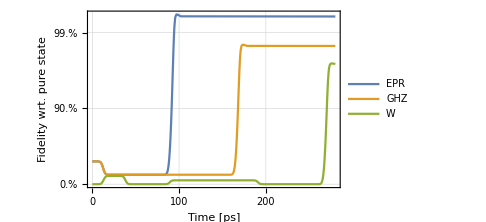

```mathematica
ListLinePlot[{fidVsTimeEPRCopy,fidVsTimeGHZCopy,fidVsTimeWCopy},PlotRange->All,GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,Ceiling[Max[fidVsTimeWCopy[[;;,2]]]]}],None},{Table[{i,Style[ToString[i],16]},{i,0,300,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]","Fidelity wrt. pure state"}}],PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],PlotStyle->Thick]
```

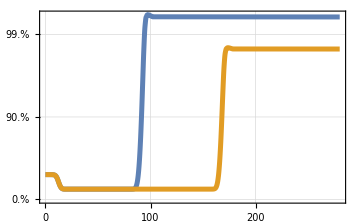

-Graphics-

```mathematica
ListLinePlot[{fidVsTimeEPRCopy,fidVsTimeGHZCopy},PlotRange->All,GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,Ceiling[Max[fidVsTimeWCopy[[;;,2]]]]}],None},{Table[{i,Style[ToString[i],16]},{i,0,300,50}],None}},(*FrameLabel->Table[Style[i,20],{i,{"Time [ps]","Fidelity wrt. pure state"}}],*)(*PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],*)PlotStyle->Table[Directive[ColorData[97][i],Thickness[0.01]],{i,1,2}]]
```

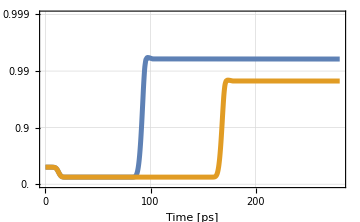

```mathematica
ListLinePlot[{fidVsTimeEPRCopy,fidVsTimeGHZCopy},PlotRange->{0,3},GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[(1-10.^(-i))],18]},{i,0,3}],None},{Table[{i,Style[ToString[i],16]},{i,0,300,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"(*,"Fidelity wrt. pure state"*)}}],(*PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],*)PlotStyle->Table[Directive[ColorData[97][i],Thickness[0.01]],{i,1,2}]]
```

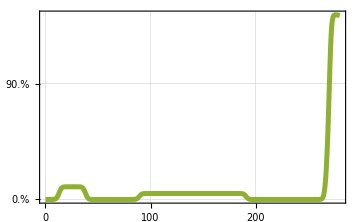

-Graphics-

```mathematica
ListLinePlot[{fidVsTimeWCopy},PlotRange->All,GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,Ceiling[Max[fidVsTimeWCopy[[;;,2]]]]}],None},{Table[{i,Style[ToString[i],16]},{i,0,300,50}],None}},(*FrameLabel->Table[Style[i,20],{i,{"Time [ps]","Fidelity wrt. pure state"}}],*)(*PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],*)PlotStyle->Table[Directive[ColorData[97][i],Thickness[0.01]],{i,{3}}]]
```

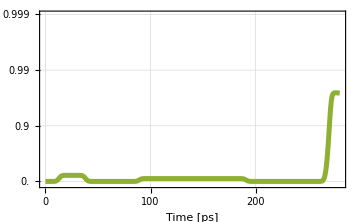

```mathematica
ListLinePlot[{fidVsTimeWCopy},PlotRange->{-0.05,3},GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[(1-10.^(-i))],18]},{i,0,3}],None},{Table[{i,Style[ToString[i],16]},{i,0,300,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"(*,"Fidelity wrt. pure state"*)}}],(*PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],*)PlotStyle->Table[Directive[ColorData[97][i],Thickness[0.01]],{i,{3}}]]
```

### Summarized fidelity evolution prep-unprep

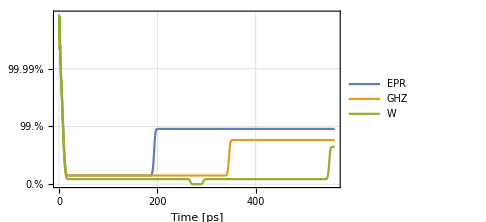

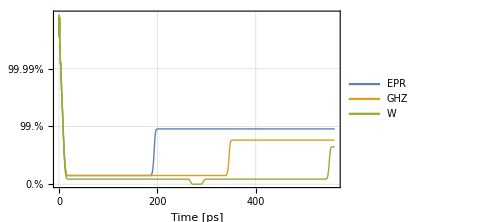

```mathematica
ListLinePlot[{fidVsTimeEPRPuPCopy,fidVsTimeGHZPuPCopy,fidVsTimeWPuPCopy},PlotRange->All,GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[100(1-10.^(-i))]<>"%",18]},{i,0,5}],None},{Table[{i,Style[ToString[i],16]},{i,0,500,100}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}],PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],PlotStyle->Thick]
```

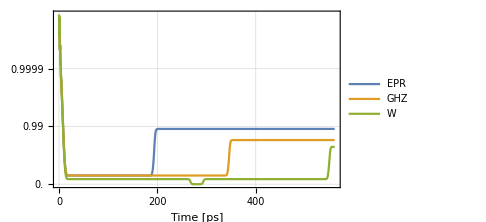

```mathematica
ListLinePlot[{fidVsTimeEPRPuPCopy,fidVsTimeGHZPuPCopy,fidVsTimeWPuPCopy},PlotRange->All,GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[(1-10.^(-i))],18]},{i,0,5}],None},{Table[{i,Style[ToString[i],16]},{i,0,500,100}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}],PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],PlotStyle->Thick]
```

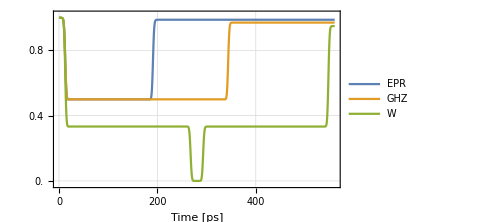

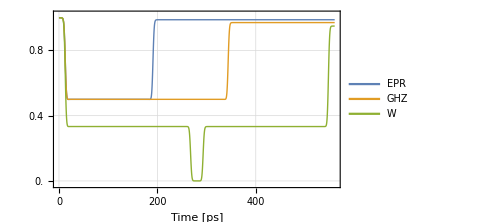

```mathematica
ListLinePlot[{fidVsTimeEPRPuP,fidVsTimeGHZPuP,fidVsTimeWPuP},PlotRange->{-0.02,1.02},GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{i,Style[ToString[i],18]},{i,0,1,0.2}],None},{Table[{i,Style[ToString[i],16]},{i,0,500,100}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}],PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],PlotStyle->Thick]
```

### Summarized purity evolution during state prep

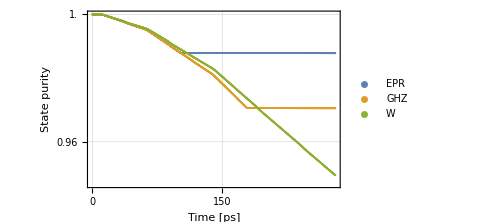

```mathematica
ListPlot[Table[Table[{p[[i,1]],Tr[p[[i,2]].p[[i,2]]]//Chop},{i,1,Dimensions[p][[1]]}],{p,{epr,ghz,w}}],PlotRange->All,GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{(1-0.02i),Style[ToString[(1-0.02i)],18]},{i,0,5}],None},{Table[{i,Style[ToString[i],16]},{i,0,500,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]","State purity"}}],PlotLegends->Placed[LineLegend[Table[ColorData[97][i],{i,1,3}],Table[Style[i,20],{i,{"EPR","GHZ","W"}}]],{Left,Bottom}]]
```

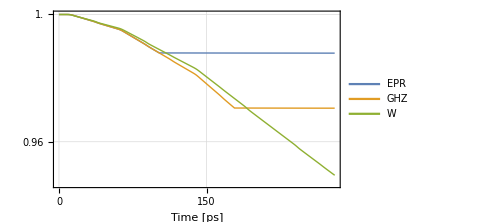

```mathematica
ListLinePlot[Table[Table[{p[[i,1]],Tr[p[[i,2]].p[[i,2]]]//Chop},{i,1,Dimensions[p][[1]]}],{p,{epr,ghz,w}}],PlotRange->All,GridLines->Automatic,ImageSize->Medium,PlotStyle->Directive[Thick],Frame->True,FrameTicks->{{Table[{(1-0.02i),Style[ToString[(1-0.02i)],18]},{i,0,5}],None},{Table[{i,Style[ToString[i],16]},{i,0,500,50}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"(*,"State purity"*)}}],PlotLegends->Placed[LineLegend[(*Table[ColorData[97][i],{i,1,3}],*)Table[Style[i,20],{i,{"EPR","GHZ","W"}}]],{Left,Bottom}]]
```

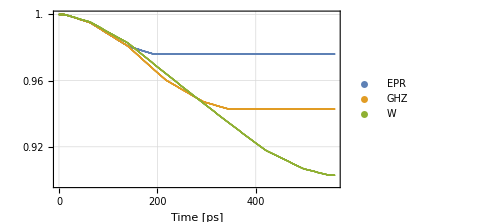

-Graphics-

```mathematica
ListPlot[Table[Table[{pup[[i,1]],Tr[pup[[i,2]].pup[[i,2]]]//Chop},{i,1,Dimensions[pup][[1]]}],{pup,{eprPuP,ghzPuP,wPuP}}],PlotRange->All,GridLines->Automatic,ImageSize->Medium,Frame->True,FrameTicks->{{Table[{(1-0.02i),Style[ToString[(1-0.02i)],18]},{i,0,5}],None},{Table[{i,Style[ToString[i],16]},{i,0,500,100}],None}},FrameLabel->Table[Style[i,20],{i,{"Time [ps]"}}],PlotLegends->Table[Style[i,18],{i,{"EPR","GHZ","W"}}],PlotStyle->Thick]
```

Final purities

```mathematica
Table[{pup[[-1,1]],Tr[pup[[-1,2]].pup[[-1,2]]]//Chop},{pup,{eprPuP,ghzPuP,wPuP}}]
```

{{560.432,0.976084},{560.432,0.942829},{560.432,0.902783}}

```mathematica
p=1-2(1+ϵ)ϵ
```

1-2 ϵ (1+ϵ)

## Saving variables

```mathematica
DumpSave["statePrepTransformError.mx",{epr,fidVsTimeEPR,fidVsTimeEPRCopy,eprTransformed,ghz,fidVsTimeGHZ,fidVsTimeGHZCopy,ghzTransformed,w,fidVsTimeW,fidVsTimeWCopy,wTransformed,eprPuP,fidVsTimeEPRPuP,fidVsTimeEPRPuPCopy,ghzPuP,fidVsTimeGHZPuP,fidVsTimeGHZPuPCopy,wPuP,fidVsTimeWPuP,fidVsTimeWPuPCopy}]
```

$Aborted[]

```mathematica
NotebookSave[]
```

## Polytope plots

```mathematica
Show[RegionPlot3D[(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1.05},{y,0.5,1.05},{z,0.5,1.05},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Green},MeshStyle->None],
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1.05},{y,0.5,1.05},{z,0.5,1.05},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Blue},MeshStyle->None],
Graphics3D[{Lighter[Red],Thickness[0.02],Line[Table[λvec[expansion5to6[epr[[128i,2]]]][[1;;3]],{i,{1,4}}]],Yellow,Ball[{1,1,1},0.02]}]]
```

-Graphics3D-

```mathematica
Show[RegionPlot3D[1≥x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1.05},{y,0.5,1.05},{z,0.5,1.05},AxesLabel->Table[Style[i,18,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Opacity[0.5],Gray},MeshStyle->None]]
```

-Graphics3D-

```mathematica
Show[RegionPlot3D[(x+y-z)≤1&&1≥x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1.05},{y,0.5,1.05},{z,0.5,1.05},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->Directive[Opacity[0.5],Lighter[Green]],MeshStyle->None],TicksStyle->Directive[Thick,18]]
```

-Graphics3D-

```mathematica
NotebookSave[]
```

```mathematica
Show[RegionPlot3D[(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->200,PlotStyle->Directive[{Opacity[0.5],Lighter[Blue,0.3]}],MeshStyle->None,TicksStyle->Directive[22]],
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->200,PlotStyle->Directive[{Opacity[0.5],Lighter[Red,0.4]}],MeshStyle->None],
Graphics3D[{Darker[Yellow,0.1],Thickness[0.01],Arrowheads[0.05],Arrow[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{1,4}}]],Arrow[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{4,7}}]],Darker[Green,0.3],Arrow[Table[λvec[expansion5to6[w[[128i,2]]]][[1;;3]],{i,{1,4,7,11}}]]}],
Graphics3D[{Text[Style[Slater,24],{1,1,1.05}],Text[Style[EPR,24],{1,0.35,0.6}],Text[Style[GHZ,24],{0.45,0.45,0.5}],Text[Style[W,24],{0.63,0.7,0.6666}]}],
ImageSize->Large,ViewPoint->{-1,-2, 1.1}]
```

-Graphics3D-

```mathematica
Show[RegionPlot3D[(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->200,PlotStyle->Directive[{Opacity[0.5],Lighter[Blue,0.3]}],MeshStyle->None,TicksStyle->Directive[22]],
RegionPlot3D[(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z&&x≥0.5&&y≥0.5&&z≥0.5,{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->200,PlotStyle->Directive[{Opacity[0.5],Lighter[Red,0.4]}],MeshStyle->None],
Graphics3D[{Darker[Yellow,0.03],Thickness[0.01],Arrowheads[0.05],Opacity[0.7],Arrow[Tube[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{1,4}}],0.005]],Arrow[Tube[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{4,7}}],0.005]],Darker[Green,0.1],Arrow[Tube[Table[λvec[expansion5to6[w[[128i,2]]]][[1;;3]],{i,{1,4,7,11}}],0.005]]}],
Graphics3D[{Text[Style[Slater,24],{1,1,1.05}],Text[Style[EPR,24],{1,0.35,0.6}],Text[Style[GHZ,24],{0.45,0.45,0.5}],Text[Style[W,24],{0.63,0.7,0.6666}]}],
ImageSize->Large,ViewPoint->{1,-2, 1.1}]
```

-Graphics3D-

```mathematica
Show[RegionPlot3D[{(x+y-z)≤1&&(x+y+z)≤2&&x≥y≥z≥0.5,(x+y-z)≤1&&(x+y+z)≥2&&x≥y≥z≥0.5},{x,0.5,1},{y,0.5,1},{z,0.5,1},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->Table[Directive[{Opacity[0.5],Lighter[col,0.3]}],{col,{Yellow,Orange}}],MeshStyle->None,TicksStyle->Directive[22],ViewPoint->{1,-2, 1}]]
```

-Graphics3D-

```mathematica
Show[RegionPlot3D[{(x+y-z)≤1&&1≥x≥y≥z≥0.5,1.08≥(x+y-z)≥1&&1≥x≥y≥z≥0.5},{x,0.5,1.01},{y,0.5,1.01},{z,0.5,1.01},AxesLabel->Table[Style[i,24,Bold],{i,{λ1,λ2,λ3}}],PlotPoints->100,PlotStyle->{Directive[Opacity[0.2],Lighter[Green]],Directive[Opacity[0.6],Lighter[Red]]},MeshStyle->None,TicksStyle->Directive[Thick,18],ViewPoint->{1,-2, 1},ImageSize->Medium](*,
Graphics3D[{Darker[Yellow,0.03],Thickness[0.01],Arrowheads[0.02],Opacity[0.7],Arrow[Tube[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{1,4}}],0.002]],Arrow[Tube[Table[λvec[expansion5to6[ghz[[128i,2]]]][[1;;3]],{i,{4,7}}],0.002]],Darker[Green,0.1],Arrow[Tube[Table[λvec[expansion5to6[w[[128i,2]]]][[1;;3]],{i,{1,4,7,11}}],0.002]]}]*)]
```

-Graphics3D-

```mathematica
λvec[expansion5to6[epr[[-1,2]]]][[1;;3]]
```

{1.,0.50122,0.501092}

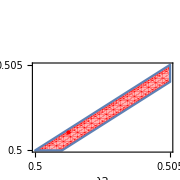

```mathematica
Show[RegionPlot[y<x&&y>x-0.001,{x,0.5,0.505},{y,0.5,0.505},AxesLabel->Automatic,ImageSize->Small,Frame->True,FrameLabel->Table[Style[i,18],{i,{λ2,λ3}}],FrameTicks->{{{0.5,0.505},None},{{0.5,0.505},None}},FrameTicksStyle->16,PlotStyle->Directive[Red,Opacity[0.3]],MeshStyle->None],Graphics[{Red,PointSize[Large],Point[{0.5012204355709299,0.5010920856560546}],Text[Style["λ1=1",18,Gray],{0.503,0.507}]}]]
```

## Examine the spectrum and natural occupation numbers of a mixed state.

```mathematica
Dimensions[epr[[-1,2]]]
```

{75,75}

```mathematica
F1[λ_]:=λ[[1]]+λ[[2]]-λ[[3]];
F2[λ_]:=λ[[1]]+λ[[2]]+λ[[4]];
```

#### EPR state

```mathematica
Eigenvalues[epr[[-1,2]]]//Chop
```

{0.99389,0.00580239,0.000104278,0.00010237,0.000101228,-3.34611×10^-6,3.11097×10^-6,-1.01569×10^-7,9.40111×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ϵepr=0.0058
```

0.0058

```mathematica
λepr=λvec[expansion5to6[epr[[-1,2]]]]
```

{1.,0.50122,0.501092,0.498778,0.498686,0.}

```mathematica
F1[λepr]
F2[λepr]
```

1.00013

2.

```mathematica
F1[λepr]<1+ϵepr
F2[λepr]<2+ϵepr
```

True

True

#### GHZ state

```mathematica
Eigenvalues[ghz[[-1,2]]]//Chop
```

{0.985061,0.0143309,0.000107768,0.000106974,0.000104076,0.000102777,0.00010126,0.000101213,-7.08725×10^-6,-5.39487×10^-6,-3.38185×10^-6,-3.2437×10^-6,3.14269×10^-6,2.18524×10^-8,2.13172×10^-8,2.06879×10^-8,-1.1895×10^-9,-6.89957×10^-10,-3.72772×10^-10,-2.8124×10^-10,-2.47048×10^-10,1.7805×10^-10,-1.03266×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ϵghz=0.0143
```

0.0143

```mathematica
λghz=λvec[expansion5to6[ghz[[-1,2]]]]
```

{0.501282,0.501084,0.500264,0.499519,0.498717,0.498695}

```mathematica
F1[λghz]
F2[λghz]
```

0.502101

1.50188

```mathematica
F1[λghz]<1+ϵghz
F2[λghz]<2+ϵghz
```

True

True

#### W state

```mathematica
Eigenvalues[w[[-1,2]]]//Chop
```

{0.97423,0.0165606,0.00812194,0.00035352,0.000279822,0.000133444,0.0000980454,0.0000700425,0.0000684041,0.0000599103,0.0000313465,-9.20356×10^-6,-5.63444×10^-6,4.35345×10^-6,-3.6879×10^-6,2.61607×10^-6,2.18092×10^-6,2.14721×10^-6,1.43596×10^-6,-1.31339×10^-6,5.81271×10^-8,4.29551×10^-8,4.25914×10^-8,4.15283×10^-8,1.41697×10^-8,1.38359×10^-8,1.38028×10^-8,-2.22595×10^-9,1.95903×10^-9,-1.49028×10^-9,9.85093×10^-10,-7.45894×10^-10,7.08046×10^-10,5.22164×10^-10,-4.75068×10^-10,4.29525×10^-10,-3.44578×10^-10,2.96848×10^-10,2.82972×10^-10,2.76307×10^-10,2.75641×10^-10,1.94132×10^-10,-1.60105×10^-10,-1.57088×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ϵw=0.0166
```

0.0166

```mathematica
λw=λvec[expansion5to6[w[[-1,2]]]]
```

{0.666962,0.666608,0.665947,0.333484,0.33324,0.333037}

```mathematica
F1[λw]
F2[λw]
```

0.667623

1.66705

```mathematica
F1[λw]<1+ϵw
F2[λw]<2+ϵw
```

True

True

## Examine the occupation numbers and see if they satisfy one electron per DQD

#### EPR state

On the first, second and third DQD

```mathematica
onebrdmepr=Chop[OneBRDM[expansion5to6[epr[[-1,2]]]]];
onebrdmepr//MatrixForm
Total[Table[onebrdmepr[[i,i]],{i,{1,2}}]]
Total[Table[onebrdmepr[[i,i]],{i,{3,4}}]]
Total[Table[onebrdmepr[[i,i]],{i,{5,6}}]]
```

(0.50005 | -2.6394×10^-6-0.00119209 ⅈ | 0 | 0 | 0 | 0
-2.6394×10^-6+0.00119209 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | -2.7584×10^-6+0.0011921 ⅈ | 0 | 0
0 | 0 | -2.7584×10^-6-0.0011921 ⅈ | 0.499735 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0)

0.999778

0.999999

1.

#### GHZ state

On the first, second and third DQD

```mathematica
onebrdmghz=Chop[OneBRDM[expansion5to6[ghz[[-1,2]]]]];
onebrdmghz//MatrixForm
Total[Table[onebrdmghz[[i,i]],{i,{1,2}}]]
Total[Table[onebrdmghz[[i,i]],{i,{3,4}}]]
Total[Table[onebrdmghz[[i,i]],{i,{5,6}}]]
```

(0.50005 | -2.62077×10^-6-0.00118368 ⅈ | 0 | 0 | 0 | 0
-2.62077×10^-6+0.00118368 ⅈ | 0.499729 | 0 | 0 | 0 | 0
0 | 0 | 0.500264 | 2.8459×10^-6+1.05444×10^-8 ⅈ | 0 | 0
0 | 0 | 2.8459×10^-6-1.05444×10^-8 ⅈ | 0.499519 | 0 | 0
0 | 0 | 0 | 0 | 0.500473 | -2.75721×10^-6+0.00119161 ⅈ
0 | 0 | 0 | 0 | -2.75721×10^-6-0.00119161 ⅈ | 0.499525)

0.999778

0.999783

0.999999

#### W state

On the first, second and third DQD

```mathematica
onebrdmw=Chop[OneBRDM[expansion5to6[w[[-1,2]]]]];
onebrdmw//MatrixForm
Total[Table[onebrdmw[[i,i]],{i,{1,2}}]]
Total[Table[onebrdmw[[i,i]],{i,{3,4}}]]
Total[Table[onebrdmw[[i,i]],{i,{5,6}}]]
```

(0.665945 | 0.0000242782+0.000849171 ⅈ | 0 | 0 | 0 | 0
0.0000242782-0.000849171 ⅈ | 0.333486 | 0 | 0 | 0 | 0
0 | 0 | 0.666606 | -4.64555×10^-7+0.000785848 ⅈ | 0 | 0
0 | 0 | -4.64555×10^-7-0.000785848 ⅈ | 0.333242 | 0 | 0
0 | 0 | 0 | 0 | 0.66696 | -1.90468×10^-6+0.000786981 ⅈ
0 | 0 | 0 | 0 | -1.90468×10^-6-0.000786981 ⅈ | 0.333039)

0.999431

0.999848

0.999999

```mathematica
NotebookSave[]
```